### This notebook processes raw OD vs time data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Moje Dokumenty\bio\turbidostat_new_design

### OD threshold for the time to regrowth for ALL data except for spike-in experiments, for which the threshold is 0.075

```mathematica
odregrowth=0.05;
```

## helper functions

```mathematica
Clear[ods,odscatt,odbkg,odraws,LBinjs,Ainjs,OUTs,vols,odcrit,dilf,SE]
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[DetectODstep]
DetectODstep[ods0_]:=Module[{fit1,fit2,ods,imax=Length[ods0]},
Do[If[ods0[[i,2]]>0.01,imax=i;Break[]],{i,Length[ods0]}];
If[imax<20,imax=20];
ods=ods0[[1;;imax]];
Sort[Table[fit1=Fit[ods[[1;;i]],{1,t},t];fit2=Fit[ods[[i+1;;]],{1,t},t];{Mean[(#[[2]]-fit1/.(t->#[[1]]))^2&/@ods[[1;;i]]]+Mean[(#[[2]]-fit2/.(t->#[[1]]))^2&/@ods[[i+1;;]]],fit2-fit1/.t->(ods[[i,1]]+ods[[i+1,1]])/2},{i,3,Length[ods]-5}]][[1,2]]]
RemoveSpikes[d_,eps_:0.005]:=Module[{diff=Abs[Differences[d[[All,2]]]]},Select[Table[{d[[i]],If[i<Length[d]-1,If[diff[[i+1]]<eps && diff[[i]]<eps,True,False],If[diff[[i-1]]<eps,True,False]]},{i,Length[d]}],(#[[2]])&][[All,1]]]
Clear[DeNoise]
DeNoise[data_,th_:0.1]:=Module[{d=data,inds={}},
Do[
inds={};
Do[
If[Abs[d[[i-1,2]]-d[[i,2]]]>th || Abs[d[[i+1,2]]-d[[i,2]]]>th,AppendTo[inds,{i}]]
,{i,2,Length[d]-1}];
If[Length[inds]>0,d=Delete[d,inds],Break[]];
,{st,10}];
(*ListPlot[{data,d}]]*)
d]
Clear[LoadData,ProcessData]
LoadData[f1_,f2_:0,maxtime_:0]:=Module[{names,configfile,filename,configname,log,config,vols,conc0,dilf,odcrit,ods,odraws,odbkg,LBinjs,Ainjs,OUTs,odscatt,temp},SetDirectory[NotebookDirectory[]];
If[f2==0,
names=FileNames[f1<>"\\*"];
If[Length[names]==0 (* when only date is provided*),
names=FileNames["ODvsTime\\"<>f1<>"*\\*.txt"];

,Print["cannot find any files for ",f1];Interrupt[]];
configname=Select[names,StringContainsQ[#,"config"]&][[1]];
filename=Sort[names,(FileByteCount[#1]>FileByteCount[#2])&][[1]];
,
filename=f1;configname=f2;
];
Print[filename];
If[StringQ[filename] && FileExistsQ[filename] && FileExistsQ[configname],
log=Select[Import[filename,"Table"][[2;;]],(Length[#]>0)&];
Print[Length[log]];
log[[All,1]]/=3600.;(*convert time to hours *)
If[maxtime>0,log=Select[log,(#[[1]]<maxtime)&]];

config=Import[configname,"Table"];
vols=config[[8;;11,2]];
conc0=config[[7,2]];
dilf=config[[5,2]];
odcrit=config[[6,2]];
,log={};Print["files not found: ",filename," ",configname];Abort[]
];


If[Length[log]>0,
ods=Table[Select[log,(#[[2]]=="ODcorr" && #[[3]]==n)&][[All,{1,4}]],{n,0,3}];
odraws=Table[Select[log,(#[[2]]=="OD" && #[[3]]==n )&][[All,{1,4}]],{n,0,3}];
odbkg=Table[Select[log,(#[[2]]=="ODcorr" && #[[3]]==n)&][[All,{1,5}]],{n,0,3}];
LBinjs=Table[Select[log,(#[[2]]=="LB" && #[[3]]==n)&][[All,{1,4}]],{n,0,3}];
Ainjs=Table[Select[log,(#[[2]]=="AB" && #[[3]]==n)&][[All,{1,4}]],{n,0,3}];
OUTs=Table[Select[log,(#[[2]]=="OUT" && #[[3]]==n)&][[All,{1,4}]],{n,0,3}];
odscatt=Table[Select[log,(#[[2]]=="SC" )&][[All,{1,3+2n}]],{n,0,3}];
temp=Select[log,(#[[2]]=="LT" )&][[All,{1,4}]];

Table[<|"vol"->vols[[n]],"ods"->ods[[n]],"odraws"->odraws[[n]],"odbkg"->odbkg[[n]],"LBinjs"->LBinjs[[n]],"Ainjs"->Ainjs[[n]],"outs"->OUTs[[n]],"odscatter"->odscatt[[n]],"n"->n,"filename"->filename,"configname"->configname,"dilf"->dilf,"odcrit"->odcrit,"temp"-> temp|>,{n,1,4}]
]]

(* processes raw data, saves ODs in text files in the same directory where raw data is *)
ProcessData[data_,odrif0_:0,odrifslope_:0]:=Module[{dir=FileNameDrop[data[["filename"]],-1],ods=Select[data⟦"ods"⟧,(NumberQ[#[[2]]])&],odraws=Select[data⟦"odraws"⟧,(NumberQ[#[[2]]])&],outs=data[["outs"]],grrates,Ainjs=data[["Ainjs"]],n=data[["n"]],dilf=data["dilf"],odcrit=data["odcrit"],seq},
Export[dir<>"\\OD_vs_time_culture_"<>ToString[n]<>".txt",SetPrecision[ods,4],"Table"];
grrates=Module[{od,fit,fun,grr={},c0=0,b0=1,dd},
od=Select[Table[seq=Select[odraws,(#[[1]]>outs[[i,1]] && #[[1]]<outs[[i+1,1]])&];If[Length[seq]>2,seq[[1;;-2]],{}],{i,2,Length[outs]-1}],(Length[#]>1)&];
If[odrif0!=0,od=Table[{#[[1]],If[#[[1]]>Ainjs[[1,1]],#[[2]]-odrif0-odrifslope(#[[1]]-od[[i,1,1]]),#[[2]]]}&/@od[[i]],{i,Length[od]}]];
Print[dir," culture=",n," cycles=",Length[od]];
Do[
fun=c+If[t<od[[i,1,1]],a,dilf a]Exp[b (t-od[[i-1,1,1]])]; (* growth rate determined this way interpolates between g.rates in two consecutive cycles *)
dd=Join[od[[i-1]],od[[i]]]; (* join data from two consecutive cycles *)
fit=FindFit[dd,fun,{{a,odcrit},{b,b0},{c,c0}},t,MaxIterations->100]; (* fit, using best-fit params from the previous pair of cycles as the initial conditon *)
If[(b/.fit)>0 && (b/.fit)<3,b0=b/.fit;c0=c/.fit];
AppendTo[grr,{od[[i,1,1]],b/.fit,Total[(#[[2]]-fun/.fit/.t->#[[1]])^2&/@od[[i,All]]]/Mean[od[[i,All,2]]]^2,(* OD max in the same time period *)Max[Select[ods,(#[[1]]>=od[[i,1,1]] && #[[1]]<od[[i,-1,1]])&][[All,2]]], (* OD_background estimated from the fit *)c/.fit}];
,{i,2,Length[od]}];
grr
];
grrates
]
```

## RIF alone, no bacteria

### Some problem with culture 0 but it is still included

ODvsTime\20241206_rif_test_no_cells\log2024-12-6_11h17m28s.txt

62266

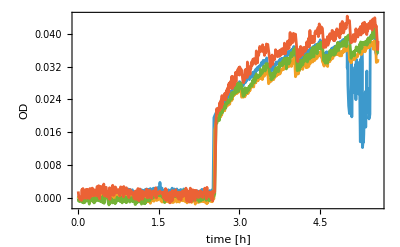

```mathematica
data0=LoadData["20241206_rif_test_no_cells",0,20];
ListPlot[data0[[All,2]],Joined->True,FrameLabel->{"time [h]","OD"},Frame->True]
```

### Simple model of RIF decay kinetics

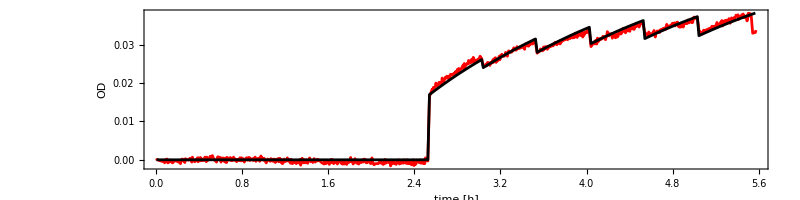

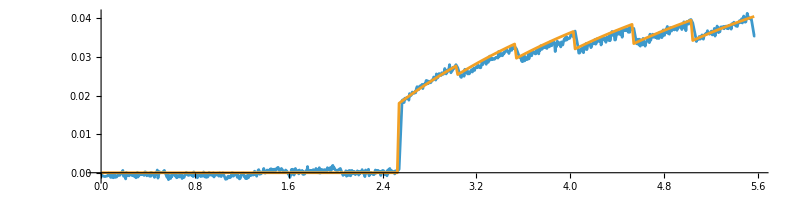

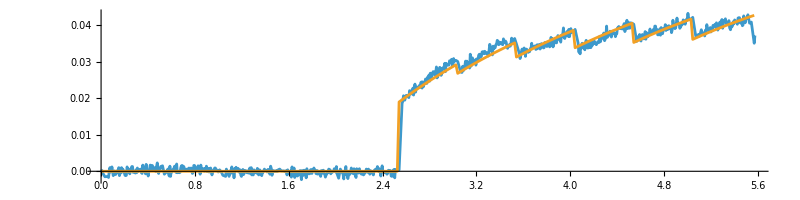

```mathematica
Clear[thOD]
thOD[dilf_,rif0_,λ_,wdecay_]:=Module[{tts=data0[[2,"ods",All,1]],c=1,ainjs=data0[[2,"Ainjs",All,1]],rif=0,dec=0 (* decay product of rif*),od,dt},Table[If[tts[[i]]>ainjs[[1]] && c==1,rif=rif0;c=2];If[c>1 && tts[[i]]<ainjs[[-1]] && tts[[i]]>ainjs[[c]],rif=rif*dilf+rif0*(1-dilf);dec=dec*dilf;c++];od=rif+wdecay dec;
dt=tts[[i+1]]-tts[[i]];
rif-=λ rif*dt;
dec+=λ rif*dt;
{tts[[i]],od},{i,Length[tts]-1}]];
ListPlot[{data0[[2,2]],thOD[0.75,0.017,0.55,3.3]},PlotStyle->{Red,Black},Joined->True,ImageSize->800,AspectRatio->0.25,Frame->True,FrameLabel->{"time [h]","OD"},FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}]
ListPlot[{data0[[3,2]],thOD[0.75,0.018,0.55,3.3]},Joined->True,ImageSize->800,AspectRatio->0.25]
ListPlot[{{#[[1]],#[[2]]-0.001}&/@data0[[4,2]],thOD[0.75,0.019,0.55,3.3]},Joined->True,ImageSize->800,AspectRatio->0.25]
```

### Approximate Bayesian inference of the parameters:

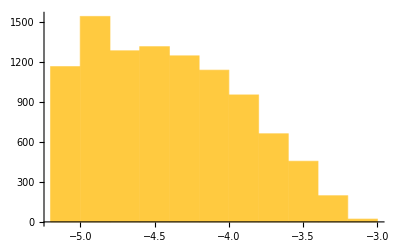

```mathematica
fits=Table[Module[{λ=0.3+RandomReal[]*0.5,r0=0.018(1+0.3RandomReal[]),wdecay=RandomReal[{2,4}],th},th=thOD[0.75,r0,λ,wdecay][[All,2]];{Mean[(data0[[2,2,;;-2,2]]-th)^2]+Mean[(data0[[3,2,;;-2,2]]-th)^2]+Mean[(data0[[4,2,;;-2,2]]-0.001-th)^2],r0,λ,wdecay}],{10000}];
Histogram[Log[10,fits[[All,1]]],10]
```

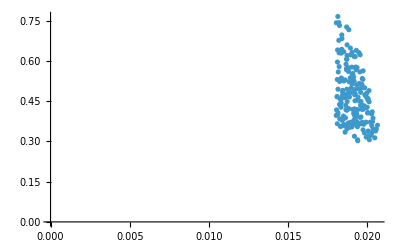

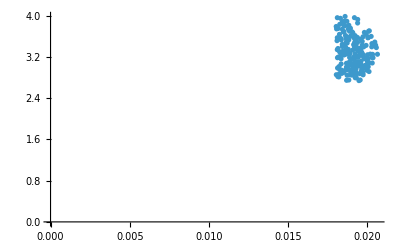

```mathematica
cutoff=7.5 10^-6;
ListPlot[Select[fits,(#[[1]]<cutoff)&][[All,{2,3}]],PlotRange->{{0,All},{0,All}}]
ListPlot[Select[fits,(#[[1]]<cutoff)&][[All,{2,4}]],PlotRange->{{0,All},{0,All}}]
```

```mathematica
(* mean parameter values and their SD *)
Mean[Select[fits,(#[[1]]<cutoff)&][[All,{2,3,4}]]]
StandardDeviation[Select[fits,(#[[1]]<cutoff)&][[All,{2,3,4}]]]
```

{0.0191089,0.469416,3.29127}

{0.000657804,0.105382,0.31438}

### We take “wdecay” to be 3.3. This is then hard-coded in all C++ simulations.

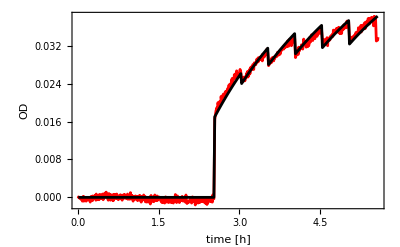

figures\RIF_model_fit.png

```mathematica
ListPlot[{data0[[2,2]],thOD[0.75,0.017,0.55,3.3]},PlotStyle->{Red,Black},Joined->True,ImageSize->400,Frame->True,FrameLabel->{"time [h]","OD"},FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},BaseStyle->FontSize->24]
Export["figures\\RIF_model_fit.png",%,"PNG"]
```

### mind that the decay rate can be different with/without bacteria, so this parameter will have to be estimated separately for each culture

## RIF, long runs

```mathematica
data=Catenate[{
LoadData["20200819"],
LoadData["20200821"],
LoadData["20200826"],
LoadData["20200828"],
LoadData["20220610"],
LoadData["20220921"]}];
```

ODvsTime\20200819\20200819_AD30_AD30YFP_RIF.txt

68638

ODvsTime\20200821\20200821_AD30_AD30YFP_RIF.txt

251816

ODvsTime\20200826\20200826_AD30_AD30YFP_rif.txt

78565

ODvsTime\20200828\20200828_AD30_AD30YFP_rif.txt

68779

ODvsTime\20220610\log2022-6-9_9h33m30s.txt

313098

ODvsTime\20220921\20220921_ev100mikrogRIF.txt

70768

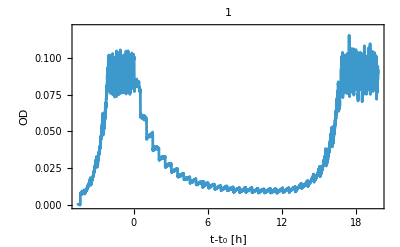
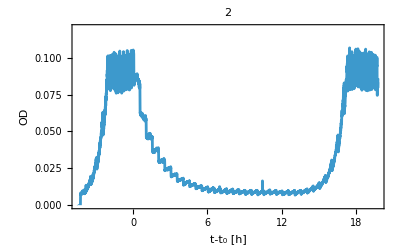
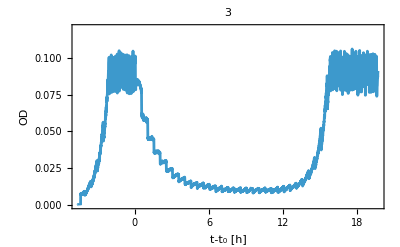
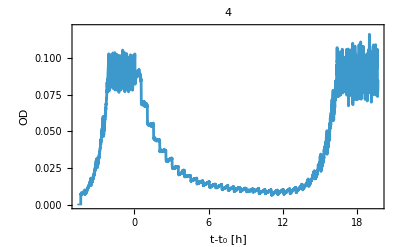
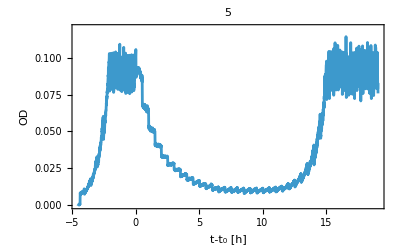
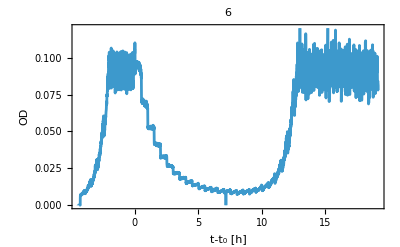
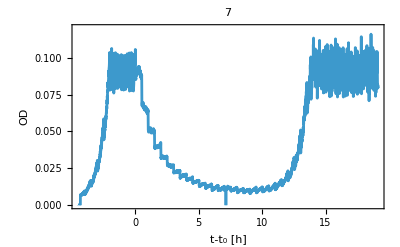
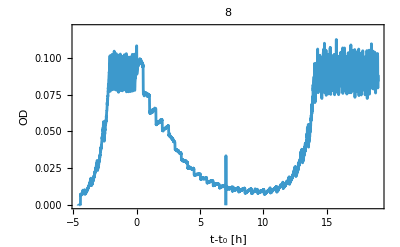

```mathematica
Table[ListPlot[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@data[[k,"ods"]],PlotLabel->ToString[k],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}],{k,Length[data]}]
```

```mathematica
(* this delete experiments that stopped too early to be conclusive *)
data2=Delete[data,{{9}}];
data=data2;
dataprev=data;
Length[data]
```

23

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_rif_long_runs_ODvsTIME.mx",data]; (* this is the uncorrected data, which won't be used for modelling *)
```

#### The problem with these data is that the OD background correction was incorrect. This was fixed from Nov 2022. Also, RIF contributes to the optical density because it is a dye that absorbs at 600 nm (wavelength used for OD measurement). So this needs to be corrected for for all experiments before Nov 2022, including all RIF

#### We settled on the approach that fits each curve separately using the RIF addition and decay model. This code does it for all curves, and creates the corrected data structure

```mathematica
Clear[CorrectForRIF]
CorrectForRIF[data_,λ_,rif0_,t1_:0,t2_:100]:=Module[{tts=Select[data[["ods",All,1]],(#<t2)&],ods=data[["ods",All,2]],odraws=data[["odraws",All,2]],odbkg=data[["odbkg"]],c=1,ainjs=data[["Ainjs",All,1]],rif=0,dec=0 (* decay product of rif*),od,dt,dilf=0.75},Table[If[tts[[i]]>ainjs[[1]] && c==1,rif=rif0;c=2];If[c>1 && tts[[i]]<ainjs[[-1]] && tts[[i]]>ainjs[[c]],rif=rif*dilf+rif0*(1-dilf);dec=dec*dilf;c++];od=rif+3.3dec;
If[i<Length[tts],dt=tts[[i+1]]-tts[[i]]];
rif-=λ rif*dt;
dec+=λ rif*dt;
{tts[[i]],odraws[[i]]-od-odbkg[[1,2]],odraws[[i]]-od},{i,Length[tts]}]];
Clear[fitting]
fitting[k_,λ_,rif0_]:=Module[{ods=CorrectForRIF[dataprev[[k]],λ,rif0][[All,{1,2}]],odssel},odssel=Select[ods,(#[[1]]>dataprev[[k,"Ainjs",1,1]]+8 && #[[1]]<dataprev[[k,"Ainjs",1,1]]+10)&];Sqrt[Variance[odssel[[All,2]]]]+Max[0,-Mean[odssel[[All,2]]]]+0.1Abs[Mean[odssel[[All,2]]]]]
```

1{0.00038417,0.15,0.024}

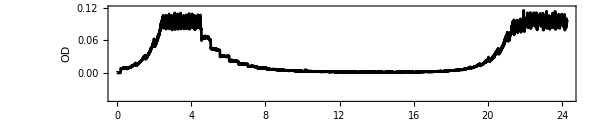

2{0.000407979,0.175,0.024}

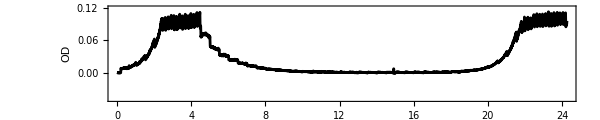

3{0.000416524,0.15,0.024}

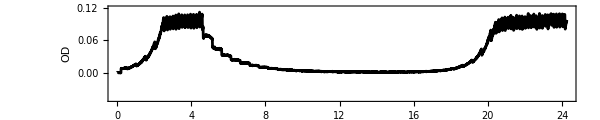

4{0.00055491,0.175,0.024}

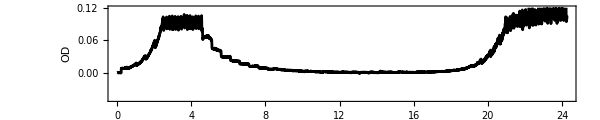

5{0.000556973,0.15,0.032}

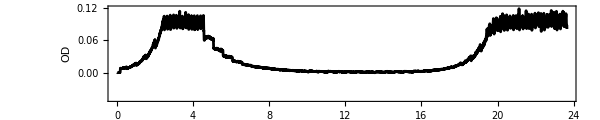

6{0.000840609,0.15,0.032}

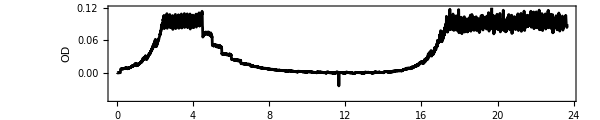

7{0.000614872,0.15,0.032}

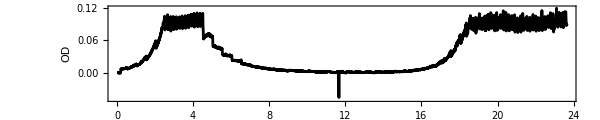

8{0.000567446,0.15,0.032}

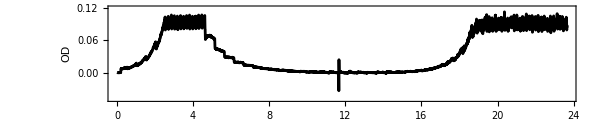

9{0.000235454,0.2,0.02}

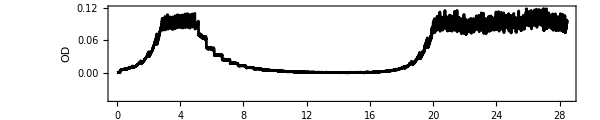

10{0.000317929,0.175,0.02}

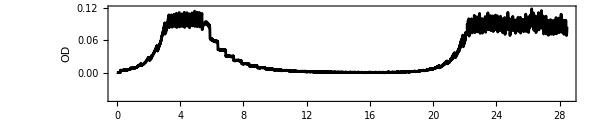

11{0.000307411,0.175,0.02}

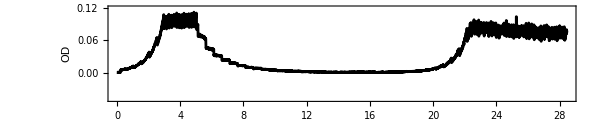

12{0.000507127,0.175,0.026}

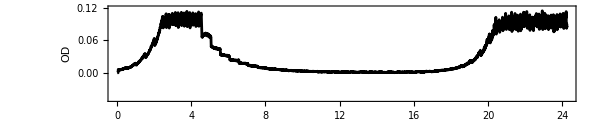

13{0.000506848,0.15,0.026}

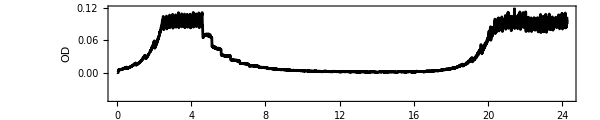

14{0.000573317,0.15,0.026}

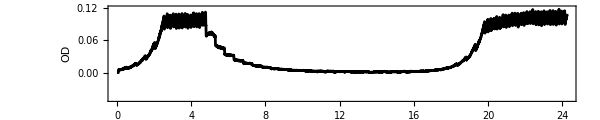

15{0.000412011,0.15,0.026}

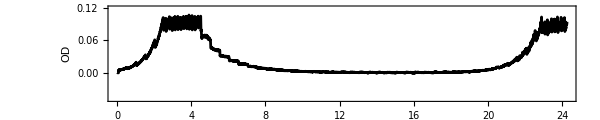

16{0.000340165,0.175,0.018}

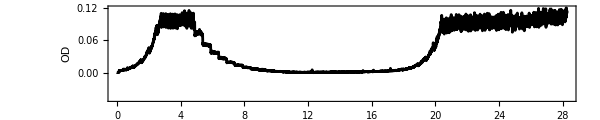

17{0.000452805,0.15,0.02}

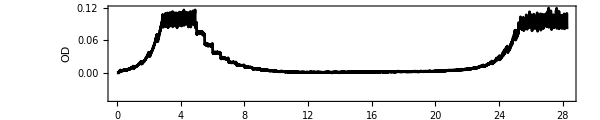

18{0.000352652,0.2,0.018}

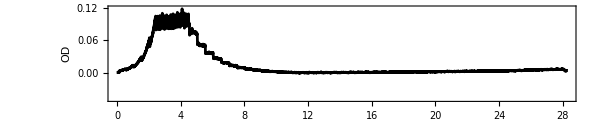

19{0.000616793,0.15,0.018}

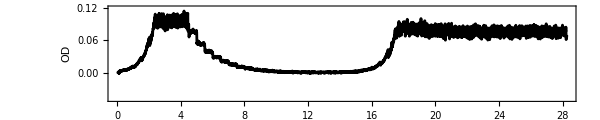

20{0.00115366,0.15,0.016}

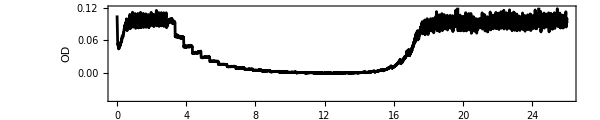

21{0.000317236,0.2,0.016}

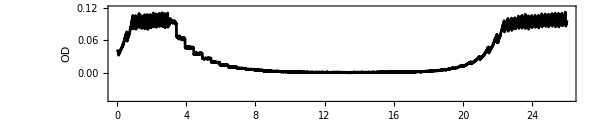

22{0.000592332,0.175,0.016}

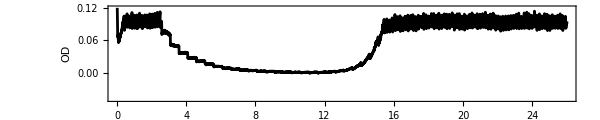

23{0.000857466,0.175,0.016}

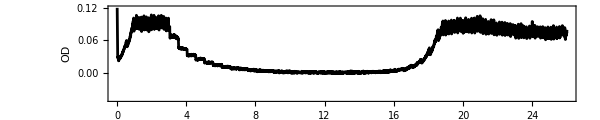

```mathematica
data=dataprev;
bestfits={};
Do[
bestfit=Sort[Flatten[Table[{fitting[k,λ,r0],λ,r0},{λ,0.15,0.25,0.025},{r0,0.016,0.04,0.002}],1]][[1]];
Print[k,bestfit];
AppendTo[bestfits,bestfit];
corrected=CorrectForRIF[dataprev[[k]],bestfit[[2]],bestfit[[3]]];
Print[ListPlot[corrected[[All,{1,2}]],PlotRange->{-0.05,0.12},Joined->True,AspectRatio->0.2,ImageSize->600,PlotStyle->Black,Frame->True,FrameLabel->{"time [h]","OD"},BaseStyle->FontSize->24,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}]];
data[[k,"ods"]]=Select[corrected[[All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[corrected[[All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&]
,{k,Length[dataprev]}]
```

### Here are the values that need to be used to model all RIF data:

```mathematica
Mean[bestfits]
```

{0.000516813,0.165217,0.0228696}

```mathematica
RIF0=0.023;
RIFlambda=0.16;
```

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_rif_long_runs_ODvsTIME_corrected.mx",data]; (* the corrected data -this will be used for modelling *)
```

### We now calculate growth rates vs time for all RIF experiments

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20200819 culture=1 cycles=68

ODvsTime\20200819 culture=2 cycles=68

ODvsTime\20200819 culture=3 cycles=74

ODvsTime\20200819 culture=4 cycles=70

ODvsTime\20200821 culture=1 cycles=71

ODvsTime\20200821 culture=2 cycles=83

ODvsTime\20200821 culture=3 cycles=78

ODvsTime\20200821 culture=4 cycles=75

ODvsTime\20200826 culture=2 cycles=102

ODvsTime\20200826 culture=3 cycles=91

ODvsTime\20200826 culture=4 cycles=91

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ODvsTime\20200828 culture=1 cycles=72

ODvsTime\20200828 culture=2 cycles=72

ODvsTime\20200828 culture=3 cycles=75

ODvsTime\20200828 culture=4 cycles=62

ODvsTime\20220610 culture=1 cycles=103

ODvsTime\20220610 culture=2 cycles=78

ODvsTime\20220610 culture=3 cycles=67

ODvsTime\20220610 culture=4 cycles=131

ODvsTime\20220921 culture=1 cycles=98

ODvsTime\20220921 culture=2 cycles=70

ODvsTime\20220921 culture=3 cycles=111

ODvsTime\20220921 culture=4 cycles=92

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_rif_long_runs_growthrates.mx",growthrates];
```

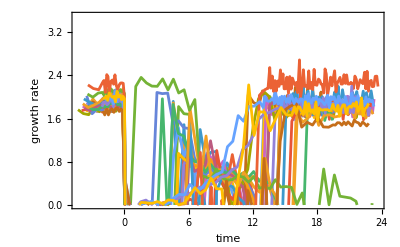

```mathematica
Print[ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],{k,Length[data]}],Joined->True,PlotRange->{0,3.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

#### T_regrowth is obtained from the corrected data, because T_regrowth from the model does not include RIF contribution, though the model simulates it to correctly model dilution times.

{24.74,26.23,24.14,25.32,25.07,26.29,24.14,25.85,25.17,24.94,25.55,24.9,25.3,24.88,25.56,25.42,24.79,24.77,26.15,25.1,25.48,24.14,26.14}

{4.50619,4.47525,4.60053,4.56925,4.55311,4.48311,4.51594,4.61958,4.92619,5.38022,5.03167,4.54533,4.59394,4.77936,4.51489,4.81117,4.90753,4.49742,4.45014,2.85561,2.93222,2.49257,2.98017}

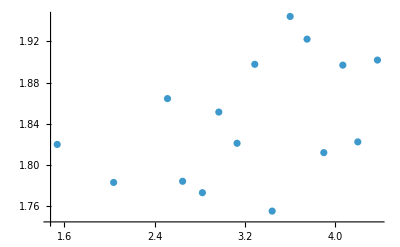
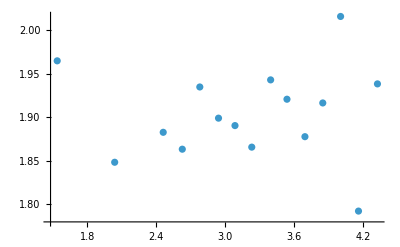
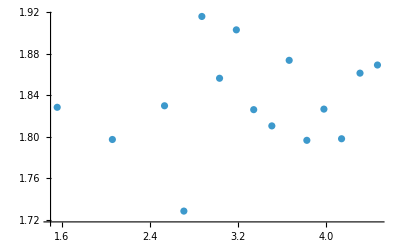
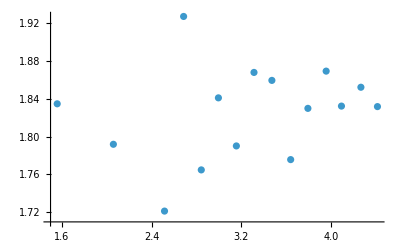
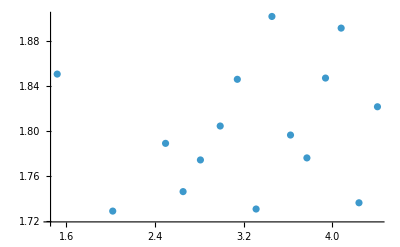
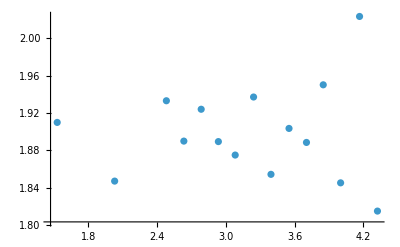
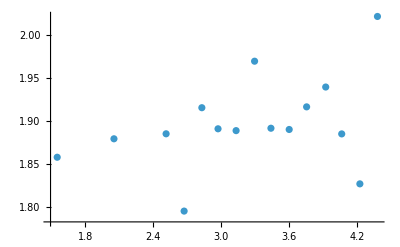
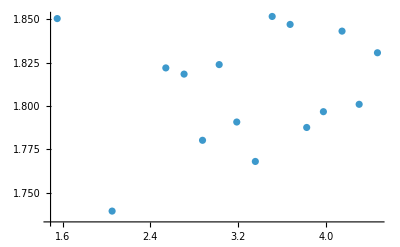

births

{{1.84322,0.0152068},{1.90349,0.0138763},{1.83476,0.0122564},{1.82596,0.0130759},{1.80243,0.0144906},{1.89916,0.0132784},{1.8967,0.0139873},{1.81002,0.00858324},{1.87714,0.0102895},{1.79405,0.0130296},{1.82706,0.0153367},{1.81684,0.0158055},{1.82339,0.0132446},{1.82716,0.0121953},{1.85157,0.012389},{1.97009,0.0134795},{2.00523,0.0187688},{2.09812,0.0104584},{2.24508,0.0243413},{1.93084,0.0238998},{1.74635,0.0127115},{1.97766,0.0166873},{2.00363,0.0140879}}

ODinis

{0.00464461,0.00400177,0.00412012,0.00448428,0.00515094,0.00412982,0.00376088,0.0044634,0.00256188,0.00225436,0.00266147,0.0050119,0.00468726,0.00431979,0.00434558,0.00266369,0.00191899,0.00281276,0.00204638,0.045956,0.0379229,0.0597045,0.0258444}

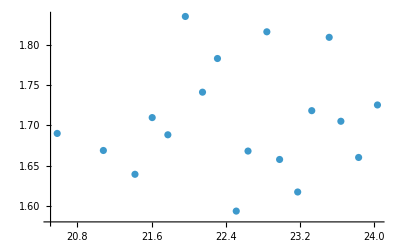
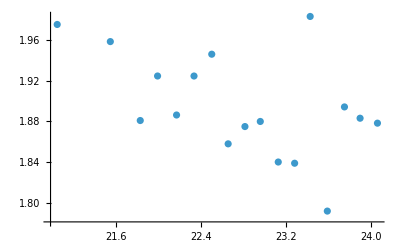
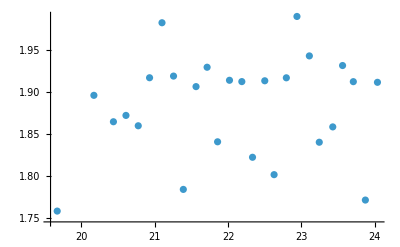
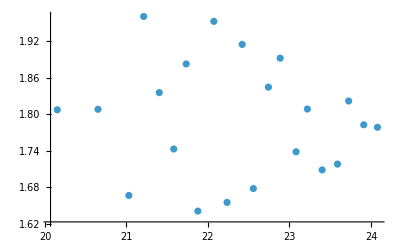
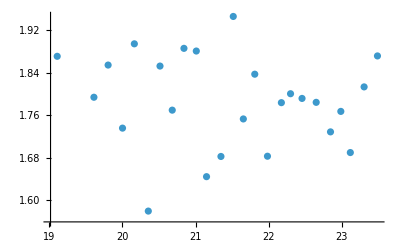
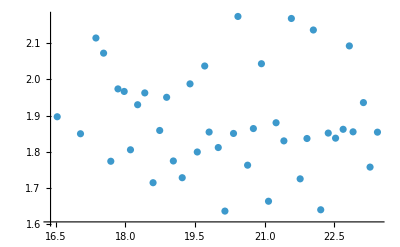
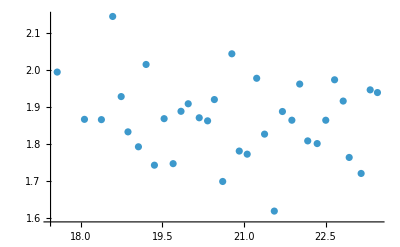
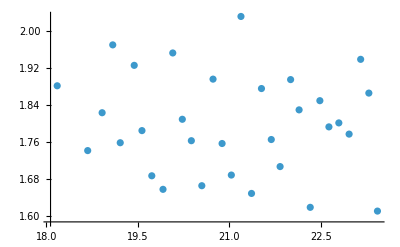
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthres

{{1.70686,0.0161615},{1.89509,0.0124488},{1.88363,0.011874},{1.79217,0.0208065},{1.7878,0.0174956},{1.88392,0.0214048},{1.86912,0.0179804},{1.79884,0.0195644},{1.85305,0.0142727},{1.7858,0.0143328},{1.78783,0.0165764},{1.79198,0.0160158},{1.80611,0.0155515},{1.86198,0.0159377},{1.69856,0.0341943},{1.91859,0.057183},{1.71954,0.0178515},{0,0},{2.26897,0.0146321},{1.86358,0.0142314},{1.50135,0.00797295},{1.93188,0.00793894},{1.77871,0.0126556}}

Tregrows

{20.8342,21.3245,19.9152,20.4595,19.2623,16.8407,17.8823,18.3482,19.7233,21.9101,21.8856,19.8833,19.8376,19.4321,22.3032,20.0352,24.7577,28.2669,17.3008,17.1475,21.71,14.9319,18.3095}

{2.45917,2.41868,2.51417,2.47639,2.45889,2.441,2.49493,2.5179,2.88481,3.25114,2.93542,2.44098,2.48191,2.51231,2.48796,2.72881,2.85906,2.39565,2.36064,0.72075,0.883053,0.397019,0.957128}

{0.000119072,-0.000868943,-0.0000289798,-0.00092164,-0.00025244,-0.0246625,-0.0461178,-0.0336257,-0.000695137,-0.000493755,-0.0000581684,-0.000304836,0.000327806,0.0000664259,-0.00103331,-0.000201212,-0.000689734,-0.000920302,-0.00168184,-0.00195329,-0.00054686,-0.000745108,-0.00203322}

{7.56356,7.538,7.66169,7.66172,7.36467,11.661,11.6611,11.6611,8.18717,8.88819,8.13817,7.58289,7.62439,7.87333,7.55842,7.90472,8.02847,7.56783,8.02858,6.86572,6.94428,6.09692,6.58311}

{24.266,24.266,24.266,24.266,23.6529,23.653,23.653,23.653,28.4731,28.4731,28.4733,24.2488,24.2488,24.2488,24.2488,28.2667,28.2667,28.2669,28.2669,26.0127,26.0128,26.0128,26.0129}

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]
Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
Print["ODinis"]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[Module[{gr={},i=Length[growthrates[[k]]]},While[growthrates[[k,i,4]]>0.05,AppendTo[gr,growthrates[[k,i,{1,2}]]];i--]; gr],PlotRange->All],{k,Length[data]}]
Print["birthres"]
birthsres=Table[Module[{gr={},i=Length[growthrates[[k]]]},
While[growthrates[[k,i,4]]>0.05,AppendTo[gr,growthrates[[k,i,2]]]i--];If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
Print["Tregrows"]
tregrowths=Table[Module[{i=Length[data[[k,"ods"]]],odcrit=data[[k,"odcrit"]],dilf=data[[k,"dilf"]]},While[data[[k,"ods",i,2]]>odregrowth,i--];data[[k,"ods",i,1]]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

```mathematica
Mean[tregrowths]
```

20.1001

### Export data to files that can be processed later:

```mathematica
bottlenumbers=Delete[Table[Mod[i-1,4],{i,24}],{{9}}]
```

{0,1,2,3,0,1,2,3,1,2,3,0,1,2,3,0,1,2,3,0,1,2,3}

```mathematica
Export["LB_and_RIF_growth_rates_end_point.txt",Join[{{"name","bottle","LB_growth_rate","RIF_growth_rate"}},Table[{data[[i,"filename"]],bottlenumbers[[i]],births[[i,1]],birthsres[[i,1]]},{i,Length[birthsres]}]],"TSV"]
```

LB_and_RIF_growth_rates_end_point.txt

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\turb_rif_long_runs.mx",alldata]
```

{{{24.74,26.23,24.14,25.32,25.07,26.29,24.14,25.85,25.17,24.94,25.55,24.9,25.3,24.88,25.56,25.42,24.79,24.77,26.15,25.1,25.48,24.14,26.14},{4.50619,4.47525,4.60053,4.56925,4.55311,4.48311,4.51594,4.61958,4.92619,5.38022,5.03167,4.54533,4.59394,4.77936,4.51489,4.81117,4.90753,4.49742,4.45014,2.85561,2.93222,2.49257,2.98017},{{1.84322,0.0152068},{1.90349,0.0138763},{1.83476,0.0122564},{1.82596,0.0130759},{1.80243,0.0144906},{1.89916,0.0132784},{1.8967,0.0139873},{1.81002,0.00858324},{1.87714,0.0102895},{1.79405,0.0130296},{1.82706,0.0153367},{1.81684,0.0158055},{1.82339,0.0132446},{1.82716,0.0121953},{1.85157,0.012389},{1.97009,0.0134795},{2.00523,0.0187688},{2.09812,0.0104584},{2.24508,0.0243413},{1.93084,0.0238998},{1.74635,0.0127115},{1.97766,0.0166873},{2.00363,0.0140879}},{0.00464461,0.00400177,0.00412012,0.00448428,0.00515094,0.00412982,0.00376088,0.0044634,0.00256188,0.00225436,0.00266147,0.0050119,0.00468726,0.00431979,0.00434558,0.00266369,0.00191899,0.00281276,0.00204638,0.045956,0.0379229,0.0597045,0.0258444},{{1.70686,0.0161615},{1.89509,0.0124488},{1.88363,0.011874},{1.79217,0.0208065},{1.7878,0.0174956},{1.88392,0.0214048},{1.86912,0.0179804},{1.79884,0.0195644},{1.85305,0.0142727},{1.7858,0.0143328},{1.78783,0.0165764},{1.79198,0.0160158},{1.80611,0.0155515},{1.86198,0.0159377},{1.69856,0.0341943},{1.91859,0.057183},{1.71954,0.0178515},{0,0},{2.26897,0.0146321},{1.86358,0.0142314},{1.50135,0.00797295},{1.93188,0.00793894},{1.77871,0.0126556}},{20.8342,21.3245,19.9152,20.4595,19.2623,16.8407,17.8823,18.3482,19.7233,21.9101,21.8856,19.8833,19.8376,19.4321,22.3032,20.0352,24.7577,28.2669,17.3008,17.1475,21.71,14.9319,18.3095},{2.45917,2.41868,2.51417,2.47639,2.45889,2.441,2.49493,2.5179,2.88481,3.25114,2.93542,2.44098,2.48191,2.51231,2.48796,2.72881,2.85906,2.39565,2.36064,0.72075,0.883053,0.397019,0.957128},{7.56356,7.538,7.66169,7.66172,7.36467,11.661,11.6611,11.6611,8.18717,8.88819,8.13817,7.58289,7.62439,7.87333,7.55842,7.90472,8.02847,7.56783,8.02858,6.86572,6.94428,6.09692,6.58311},{24.266,24.266,24.266,24.266,23.6529,23.653,23.653,23.653,28.4731,28.4731,28.4733,24.2488,24.2488,24.2488,24.2488,28.2667,28.2667,28.2669,28.2669,26.0127,26.0128,26.0128,26.0129}}}

## LB, RIF 100 ug/ml, AD30 + AD30YFP in 1 : 1, short run (2 h after OD = 0.1) with culture plating

```mathematica
data=Catenate[{LoadData["20220614"],
LoadData["20220224"],
LoadData["20211207"],
LoadData["20240306"]
}];
```

ODvsTime\20220614\log2022-6-14_11h59m28s.txt

47606

ODvsTime\20220224_spun_down_RIF\20220224_spund_down_RIF.txt

16059

ODvsTime\20211207_spun_down_RIF\20211207_platedonRIF.txt

12582

ODvsTime\20240306_spun_down_RIF100\log2024-3-6_8h22m12s.txt

43714

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_rif_short_runs_ODvsTIME.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20220614 culture=1 cycles=17

ODvsTime\20220614 culture=2 cycles=17

ODvsTime\20220614 culture=3 cycles=21

ODvsTime\20220614 culture=4 cycles=21

ODvsTime\20220224_spun_down_RIF culture=1 cycles=20

ODvsTime\20220224_spun_down_RIF culture=2 cycles=16

ODvsTime\20220224_spun_down_RIF culture=3 cycles=22

ODvsTime\20220224_spun_down_RIF culture=4 cycles=22

ODvsTime\20211207_spun_down_RIF culture=1 cycles=16

ODvsTime\20211207_spun_down_RIF culture=2 cycles=14

ODvsTime\20211207_spun_down_RIF culture=3 cycles=17

ODvsTime\20211207_spun_down_RIF culture=4 cycles=18

ODvsTime\20240306_spun_down_RIF100 culture=1 cycles=16

ODvsTime\20240306_spun_down_RIF100 culture=2 cycles=18

ODvsTime\20240306_spun_down_RIF100 culture=3 cycles=17

ODvsTime\20240306_spun_down_RIF100 culture=4 cycles=18

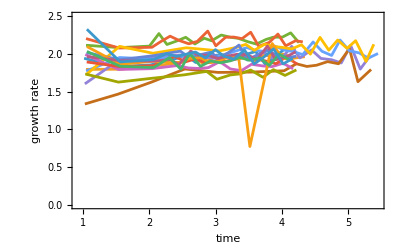

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

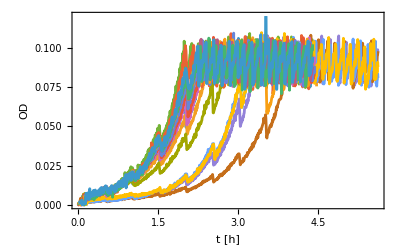

```mathematica
ListPlot[data[[All,"ods"]],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}]
```

{25.19,24.93,24.01,26.48,25.41,24.82,24.95,26.22,26.08,24.92,24.47,25.58,25.28,25.43,24.44,25.86}

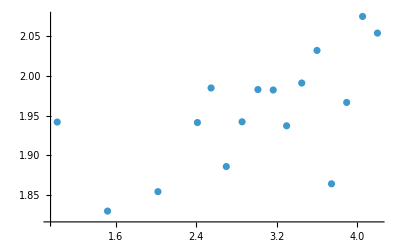
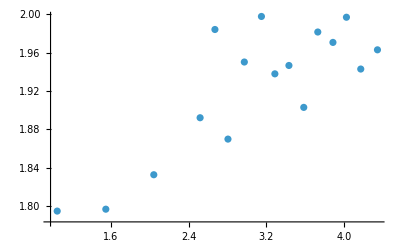
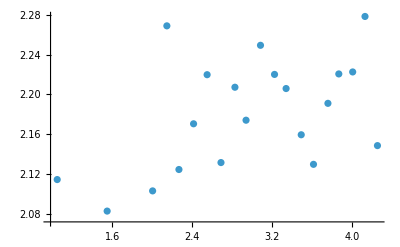
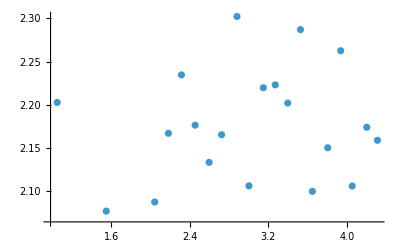
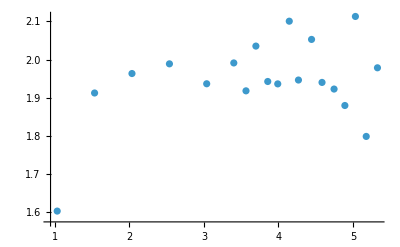
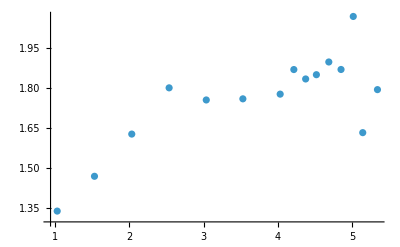
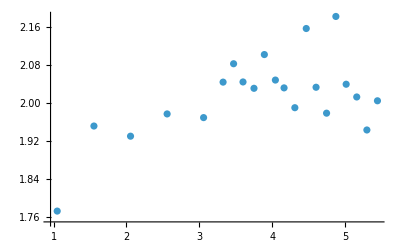
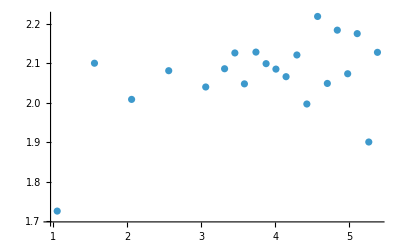

{{1.95393,0.0175378},{1.92264,0.0169112},{2.18111,0.0125475},{2.17689,0.0145476},{1.94513,0.0255052},{1.75566,0.0464592},{2.01606,0.0186416},{2.06836,0.0228598},{1.83753,0.0139176},{1.72467,0.0141818},{1.90401,0.0101991},{1.99142,0.0124397},{1.86633,0.0805219},{1.96412,0.0141813},{1.90938,0.0176119},{1.98712,0.0258596}}

{0.00398153,0.00349311,0.00435082,0.00390985,0.00108037,0.000859569,0.000998523,0.000831875,0.00502178,0.0042102,0.00456304,0.004318,0.00598778,0.00487188,0.00556088,0.00500046}

{2.38871,2.5013,1.98686,2.00969,3.38325,4.18656,3.26728,3.29631,2.41067,2.84764,2.36978,2.31172,2.27018,2.28956,2.27641,2.23945}

{4.465,4.46503,4.46511,4.46514,5.614,5.61403,5.61408,5.61414,4.43167,4.43172,4.43178,4.43183,4.39206,4.39211,4.39217,4.39222}

```mathematica
vols=data[[All,"vol"]]
Table[ListPlot[growthrates[[k]][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
births=Table[Module[{d=growthrates[[k]][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

```mathematica
alldata={vols,births,odinis,tfirstthr,tends};
DumpSave[NotebookDirectory[]<>"\\turb_rif_short_runs.mx",alldata]
```

{{{25.19,24.93,24.01,26.48,25.41,24.82,24.95,26.22,26.08,24.92,24.47,25.58,25.28,25.43,24.44,25.86},{{1.95393,0.0175378},{1.92264,0.0169112},{2.18111,0.0125475},{2.17689,0.0145476},{1.94513,0.0255052},{1.75566,0.0464592},{2.01606,0.0186416},{2.06836,0.0228598},{1.83753,0.0139176},{1.72467,0.0141818},{1.90401,0.0101991},{1.99142,0.0124397},{1.86633,0.0805219},{1.96412,0.0141813},{1.90938,0.0176119},{1.98712,0.0258596}},{0.00398153,0.00349311,0.00435082,0.00390985,0.00108037,0.000859569,0.000998523,0.000831875,0.00502178,0.0042102,0.00456304,0.004318,0.00598778,0.00487188,0.00556088,0.00500046},{2.38871,2.5013,1.98686,2.00969,3.38325,4.18656,3.26728,3.29631,2.41067,2.84764,2.36978,2.31172,2.27018,2.28956,2.27641,2.23945},{4.465,4.46503,4.46511,4.46514,5.614,5.61403,5.61408,5.61414,4.43167,4.43172,4.43178,4.43183,4.39206,4.39211,4.39217,4.39222}}}

## RIF resistant mutants, runs to measure the growth rate on LB and on 100 ug/ml RIF

#### First load an excel spreadsheet which originally did not have the growth rate columns filled (now it has thanks to the code below) This will be used to assign mutants to the OD vs time data

```mathematica
meta=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]]
muts=meta[[2;;,3]]
```

{{expriment,date,mutation,culture,LB,error,RIF,error,,ratio RIF/LB,Fit_mutant?,,,},{1.,Wed 3 Aug 2022 00:00:00GMT+1,S512P,0.,1.68396,0.00770176,1.38258,0.100467,,0.821029,0.,,,},{1.,Wed 3 Aug 2022 00:00:00GMT+1,S512P,1.,1.53236,0.0101446,1.14446,0.0165146,,0.746861,0.,,,},{1.,Wed 3 Aug 2022 00:00:00GMT+1,S512P,2.,1.89056,0.011067,1.49304,0.0944153,,0.789734,0.,,,},{1.,Wed 3 Aug 2022 00:00:00GMT+1,S512P,3.,1.99171,0.0160155,1.7165,0.0768335,,0.861822,0.,,,},{2.,Fri 5 Aug 2022 00:00:00GMT+1,S512F,0.,1.80241,0.0163057,1.5536,0.0732885,,0.861957,0.,,,},{2.,Fri 5 Aug 2022 00:00:00GMT+1,D516Y,1.,1.99908,0.018407,2.03764,0.0407605,,1.01929,1.,,,},{2.,Fri 5 Aug 2022 00:00:00GMT+1,T563P,2.,1.68159,0.0101566,0.76101,0.0346432,,0.452554,0.,,,},{3.,Wed 24 Aug 2022 00:00:00GMT+1,H526Y,0.,1.88764,0.0141006,1.91346,0.00995039,,1.01368,1.,,,},{3.,Wed 24 Aug 2022 00:00:00GMT+1,G534D,1.,1.28577,0.0069119,0.513987,0.0602976,,0.39975,0.,,,},{3.,Wed 24 Aug 2022 00:00:00GMT+1,R454P,2.,1.19505,0.00573049,0.499673,0.0640146,,0.418119,0.,,,},{4.,Thu 25 Aug 2022 00:00:00GMT+1,I572L,1.,1.71817,0.0102852,1.07787,0.0514051,,0.627336,0.,,,},{4.,Thu 25 Aug 2022 00:00:00GMT+1,Q148L,2.,1.81943,0.0199035,0.874744,0.0449972,,0.480779,0.,,,},{5.,Fri 26 Aug 2022 00:00:00GMT+1,H526D,0.,1.84011,0.0203332,1.86566,0.017977,,1.01389,1.,,,},{5.,Fri 26 Aug 2022 00:00:00GMT+1,D516G,1.,1.86841,0.0183734,1.43485,0.0339661,,0.767952,0.,,,},{5.,Fri 26 Aug 2022 00:00:00GMT+1,I572S,2.,1.9491,0.0127048,1.13081,0.0816594,,0.58017,0.,,,},{5.,Fri 26 Aug 2022 00:00:00GMT+1,H526L,3.,2.16938,0.0272181,2.16552,0.0207001,,0.998221,1.,,,},{6.,Sun 28 Aug 2022 00:00:00GMT+1,R529C,0.,0.565199,0.0164602,0.625219,0.00838698,,1.10619,0.,,,},{6.,Sun 28 Aug 2022 00:00:00GMT+1,Q513P,1.,1.23712,0.0149134,1.38641,0.0123042,,1.12068,0.,,,},{6.,Sun 28 Aug 2022 00:00:00GMT+1,S531F,2.,1.70002,0.0179544,1.73611,0.00988581,,1.02123,0.,,,},{6.,Sun 28 Aug 2022 00:00:00GMT+1,G534V,3.,1.78559,0.010953,0.735189,0.0379282,,0.411734,0.,,,},{7.,Thu 7 Mar 2024 00:00:00GMT+1,Q513L,0.,1.71756,0.00960405,1.88525,0.0174531,,1.09763,0.,,,},{7.,Thu 7 Mar 2024 00:00:00GMT+1,H526N,1.,1.90167,0.00568364,1.96703,0.0165425,,1.03437,1.,,,},{7.,Thu 7 Mar 2024 00:00:00GMT+1,S531Y,2.,1.6161,0.0136202,1.73519,0.0175161,,1.07369,0.,,,},{7.,Thu 7 Mar 2024 00:00:00GMT+1,P564R,3.,1.59997,0.00879259,1.6746,0.023378,,1.04664,0.,,,}}

{S512P,S512P,S512P,S512P,S512F,D516Y,T563P,H526Y,G534D,R454P,I572L,Q148L,H526D,D516G,I572S,H526L,R529C,Q513P,S531F,G534V,Q513L,H526N,S531Y,P564R}

```mathematica
(* select only those experiments that are in the excel table *)
Floor[meta[[2;;,{1,4}]]]
selected=(4(#[[1]]-1)+#[[2]]+1)&/@Floor[meta[[2;;,{1,4}]]]
```

{{1,0},{1,1},{1,2},{1,3},{2,0},{2,1},{2,2},{3,0},{3,1},{3,2},{4,1},{4,2},{5,0},{5,1},{5,2},{5,3},{6,0},{6,1},{6,2},{6,3},{7,0},{7,1},{7,2},{7,3}}

{1,2,3,4,5,6,7,9,10,11,14,15,17,18,19,20,21,22,23,24,25,26,27,28}

```mathematica
data=Catenate[{LoadData["20220803"],LoadData["20220805"],LoadData["20220824"],LoadData["20220825"],LoadData["20220826"],LoadData["20220828"],LoadData["20240307"]}];
```

ODvsTime\20220803\20220803_1_1.txt

20361

ODvsTime\20220805\20220805.txt

19200

ODvsTime\20220824\20220824.txt

63862

ODvsTime\20220825\20220825.txt

78232

ODvsTime\20220826\20220826.txt

19989

ODvsTime\20220828\20220828.txt

66384

ODvsTime\20240307_RifRmutants\log2024-3-7_8h22m16s.txt

86498

```mathematica
dataprev=data;
```

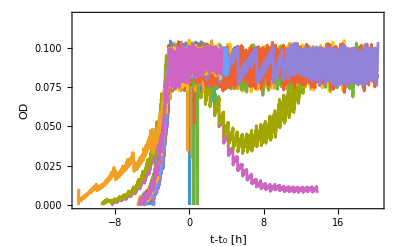

```mathematica
ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@RemoveSpikes[data[[k,"ods"]]],{k,selected}],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}]
```

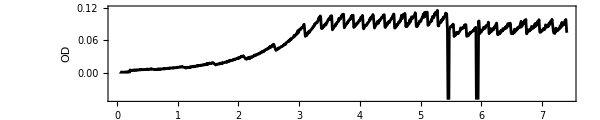

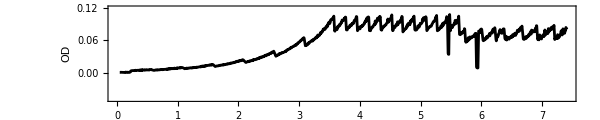

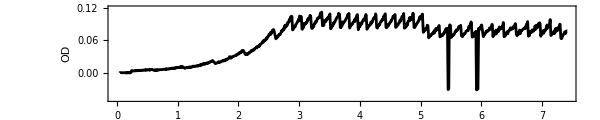

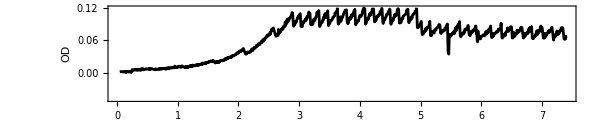

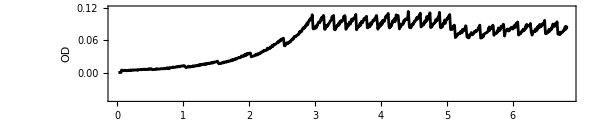

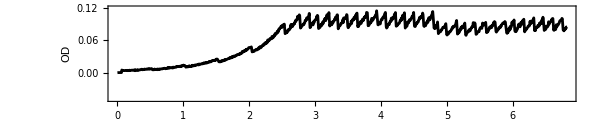

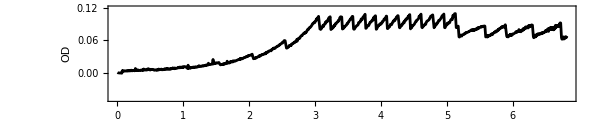

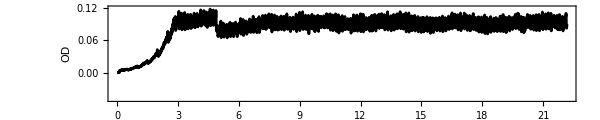

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

```mathematica
data=dataprev;
Do[
corrected=CorrectForRIF[dataprev[[k]],RIFlambda,RIF0];
Print[ListPlot[corrected[[All,{1,2}]],PlotRange->{-0.05,0.12},Joined->True,AspectRatio->0.2,ImageSize->600,PlotStyle->Black,Frame->True,FrameLabel->{"time [h]","OD"},BaseStyle->FontSize->24,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}]];
data[[k,"ods"]]=Select[corrected[[All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[corrected[[All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&]
,{k,selected}]
```

```mathematica
growthrates=ProcessData[#]&/@data[[selected]]; (* with RIF bkg correction *)
```

ODvsTime\20220803 culture=1 cycles=28

ODvsTime\20220803 culture=2 cycles=24

ODvsTime\20220803 culture=3 cycles=32

ODvsTime\20220803 culture=4 cycles=34

ODvsTime\20220805 culture=1 cycles=27

ODvsTime\20220805 culture=2 cycles=33

ODvsTime\20220805 culture=3 cycles=22

ODvsTime\20220824 culture=1 cycles=133

ODvsTime\20220824 culture=2 cycles=49

ODvsTime\20220824 culture=3 cycles=49

ODvsTime\20220825 culture=2 cycles=24

ODvsTime\20220825 culture=3 cycles=25

ODvsTime\20220826 culture=1 cycles=34

ODvsTime\20220826 culture=2 cycles=29

ODvsTime\20220826 culture=3 cycles=27

ODvsTime\20220826 culture=4 cycles=41

ODvsTime\20220828 culture=1 cycles=37

ODvsTime\20220828 culture=2 cycles=106

ODvsTime\20220828 culture=3 cycles=133

ODvsTime\20220828 culture=4 cycles=83

ODvsTime\20240307_RifRmutants culture=1 cycles=44

ODvsTime\20240307_RifRmutants culture=2 cycles=47

ODvsTime\20240307_RifRmutants culture=3 cycles=39

ODvsTime\20240307_RifRmutants culture=4 cycles=38

### Plot all growth rates versus time for different mutants :

```mathematica
Table[ListPlot[{#[[1]]-data[[selected[[k]],"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],PlotLabel->ToString[k]<>" "<>muts[[k]],Joined->True,ImageSize->240,Frame->True,FrameLabel->{"t-t_0 [h]","growth rate"},BaseStyle->FontSize->16,PlotRange->{0,2.5}],{k,Length[muts]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Average growth rates before RIF (on LB), averaged over all points with limits on max and min growth rate.

```mathematica
grsbefore=Table[Module[{d},Do[d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<data[[selected[[k]],"Ainjs",1,1]] && #[[2]]<2.5 && #[[2]]>th)&];If[Length[d]>3,Break[]],{th,{0.75,0.5,0.25}}];Print[ListPlot[{growthrates[[k,All,{1,2}]],d[[All,{1,2}]]},PlotRange->{0,2.5},Joined->
True,ImageSize->200]];{Mean[d[[All,2]]],SE[d[[All,2]]]}],{k,Length[muts]}]
```

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{1.68396,0.00770176},{1.53236,0.0101446},{1.89056,0.011067},{1.99171,0.0160155},{1.80241,0.0163057},{1.99908,0.018407},{1.68159,0.0101566},{1.88764,0.0141006},{1.28577,0.0069119},{1.19505,0.00573049},{1.71817,0.0102852},{1.81943,0.0199035},{1.84011,0.0203332},{1.86841,0.0183734},{1.9491,0.0127048},{2.16938,0.0272181},{0.565199,0.0164602},{1.23712,0.0149134},{1.70002,0.0179544},{1.78559,0.010953},{1.71756,0.00960405},{1.90167,0.00568364},{1.6161,0.0136202},{1.59997,0.00879259}}

### Average growth rates post-RIF, averaged over all points with gr > 0 and gr < 2.5 and t>0 h

```mathematica
grsafter=Table[Module[{d},Do[d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]>data[[selected[[k]],"Ainjs",1,1]]+0.25 && #[[1]]<10+data[[selected[[k]],"Ainjs",1,1]] && #[[2]]<1.2grsbefore[[k,1]] && #[[2]]>th)&];If[Length[d]>3,Break[]],{th,{0.75,0.5,0.25}}];Print[ListPlot[{growthrates[[k,All,{1,2}]],d[[All,{1,2}]]},Joined->
True,ImageSize->200,PlotRange->{0,2.5}]];{Mean[d[[All,2]]],SE[d[[All,2]]]}],{k,Length[muts]}]
```

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{1.38258,0.100467},{1.14446,0.0165146},{1.49304,0.0944153},{1.7165,0.0768335},{1.5536,0.0732885},{2.03764,0.0407605},{0.76101,0.0346432},{1.91346,0.00995039},{0.513987,0.0602976},{0.499673,0.0640146},{1.07787,0.0514051},{0.874744,0.0449972},{1.86566,0.017977},{1.43485,0.0339661},{1.13081,0.0816594},{2.16552,0.0207001},{0.625219,0.00838698},{1.38641,0.0123042},{1.73611,0.00988581},{0.735189,0.0379282},{1.88525,0.0174531},{1.96703,0.0165425},{1.73519,0.0175161},{1.6746,0.023378}}

```mathematica
TableForm[Transpose[{grsbefore[[All,1]],grsbefore[[All,2]],grsafter[[All,1]],grsafter[[All,2]]}]]
```

1.68396 | 0.00770176 | 1.38258 | 0.100467
1.53236 | 0.0101446 | 1.14446 | 0.0165146
1.89056 | 0.011067 | 1.49304 | 0.0944153
1.99171 | 0.0160155 | 1.7165 | 0.0768335
1.80241 | 0.0163057 | 1.5536 | 0.0732885
1.99908 | 0.018407 | 2.03764 | 0.0407605
1.68159 | 0.0101566 | 0.76101 | 0.0346432
1.88764 | 0.0141006 | 1.91346 | 0.00995039
1.28577 | 0.0069119 | 0.513987 | 0.0602976
1.19505 | 0.00573049 | 0.499673 | 0.0640146
1.71817 | 0.0102852 | 1.07787 | 0.0514051
1.81943 | 0.0199035 | 0.874744 | 0.0449972
1.84011 | 0.0203332 | 1.86566 | 0.017977
1.86841 | 0.0183734 | 1.43485 | 0.0339661
1.9491 | 0.0127048 | 1.13081 | 0.0816594
2.16938 | 0.0272181 | 2.16552 | 0.0207001
0.565199 | 0.0164602 | 0.625219 | 0.00838698
1.23712 | 0.0149134 | 1.38641 | 0.0123042
1.70002 | 0.0179544 | 1.73611 | 0.00988581
1.78559 | 0.010953 | 0.735189 | 0.0379282
1.71756 | 0.00960405 | 1.88525 | 0.0174531
1.90167 | 0.00568364 | 1.96703 | 0.0165425
1.6161 | 0.0136202 | 1.73519 | 0.0175161
1.59997 | 0.00879259 | 1.6746 | 0.023378

#### Now copy this to the excel spreadsheet “RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx"

## Spike-in experiments in which RifR mutant (D516Y) was mixed with the sensitive strains in approx. proportion 1:1000. 2h waiting time before RIF.

### Actual ratio very close to 1000:1 Replicate 1: problems with the OD measurements in both cultures 2 & 3, but 0 & 1 were fine. Replicate 2: problems with the OD measurements in culture 3, the rest 0,1,2 were fine. LB run out at about t=18.5h so only data points before this time are taken.

```mathematica
data=Catenate[{LoadData["20241122_1_1000_RIF",0,20][[1;;2]],LoadData["20241128_1_1000_RifR",0,18.5][[1;;3]]}];
dataprev=data;
```

ODvsTime\20241122_1_1000_RIF\log2024-11-21_9h43m12s.txt

196404

ODvsTime\20241128_1_1000_RifR\log2024-11-27_10h37m48s.txt

198708

```mathematica
ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@dataprev[[k,2]],{k,Length[data]}],Joined->True,AspectRatio->0.2,ImageSize->1200,PlotRange->{0,0.11},Frame->True]
```

-Graphics-

```mathematica
tfirstthr=Table[Module[{i=1},While[dataprev[[k,"ods",i,2]]<0.1 ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
tfirstA=Table[dataprev[[k,"Ainjs"]][[1,1]],{k,Length[data]}]
```

{2.78481,2.75998,2.47992,2.46094,2.83892}

{4.82853,4.77881,4.57775,4.47614,5.01042}

### A correction method based on the model of how RIF affects the OD. Model parameters are the same as the average parameters from the RIF mutant section.

```mathematica
data=dataprev;
data2=CorrectForRIF[#,RIFlambda,RIF0]&/@data;
Do[data[[k,"ods"]]=Select[data2[[k,All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[data2[[k,All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&],{k,Length[data]}];
```

```mathematica
ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@data[[k,2]],{k,Length[data]}],Joined->True,AspectRatio->0.2,ImageSize->1200]
```

-Graphics-

```mathematica
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_RIF_resistant_newMUT_rep1-2_1_to_1000_ODvsTIME.mx",dataprev];
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_RIF_resistant_newMUT_rep1-2_1_to_1000_ODvsTIME_corr.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20241122_1_1000_RIF culture=1 cycles=103

ODvsTime\20241122_1_1000_RIF culture=2 cycles=104

ODvsTime\20241128_1_1000_RifR culture=1 cycles=93

ODvsTime\20241128_1_1000_RifR culture=2 cycles=95

ODvsTime\20241128_1_1000_RifR culture=3 cycles=85

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

#### In the below, some function use RIF-corrected “data” and some uncorrected “dataprev” - e.g. those that depend on the actual OD such as T_regrowth. The analysis also uses a different threshold = 0.075 since the cultures rarely decayed below the threshold 0.05 used for evolutionary experiments. The analysis assumes that the simulation this is compared to adds the RIF contribution to the OD.

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]

ainjsinds=Table[Module[{i0=1},Do[If[growthrates[[n,i,1]]>ainjs[[n]],i0=i;Break[]],{i,Length[growthrates[[n]]]}];i0],{n,Length[growthrates]}] (* indices of the first growth rate post-AB *)
tregrowths=Table[Select[dataprev[[k,"ods",All]],(#[[2]]>0.075 && #[[1]]>ainjs[[k]]+2)&][[1,1]],{k,Length[dataprev]}]
trergowthsinds=Table[Module[{i0=1},Do[If[growthrates[[n,i,1]]>tregrowths[[n]],i0=i;Break[]],{i,Length[growthrates[[n]]]}];i0],{n,Length[growthrates]}] (* indices of the first growth rate post-regrowth *)

Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[growthrates[[k,-20;;-1,2]],PlotRange->All,PlotStyle->AbsolutePointSize[5]],{k,Length[data]}]
Print["birthsres"]
birthsres=Table[Module[{gr=growthrates[[k,-20;;-1,2]]},
If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[dataprev[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[dataprev]}]
ttodecay=Table[Module[{i=1,ods=dataprev[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[dataprev]}]
tends=data[[All,"ods",-1,1]]
```

{25.74,25.55,25.08,25.58,24.89}

{4.82853,4.77881,4.57775,4.47614,5.01042}

{19,19,19,18,19}

{8.77478,8.76897,8.58611,8.49839,9.37581}

{28,28,28,27,29}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

births

{{1.98877,0.0120932},{2.00071,0.0101391},{2.05494,0.0147034},{2.02345,0.0127819},{1.86728,0.0242081}}

{0.0021788,0.00229147,0.00267892,0.00291549,0.00277997}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthsres

{{2.02865,0.011482},{2.05385,0.0117563},{1.98823,0.0136899},{2.06909,0.0132719},{1.91284,0.066983}}

{2.78481,2.75998,2.47992,2.46094,2.83892}

{0.0493,0.049,0.047,0.0465,0.0454}

{6.39606,5.86294,6.11714,6.03569,6.55825}

{19.9965,19.9966,18.4878,18.4879,18.4879}

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_RIF_resistant_newMUT_rep1-2_1_to_1000.mx",alldata]
```

{{{25.74,25.55,25.08,25.58,24.89},{4.82853,4.77881,4.57775,4.47614,5.01042},{{1.98877,0.0120932},{2.00071,0.0101391},{2.05494,0.0147034},{2.02345,0.0127819},{1.86728,0.0242081}},{0.0021788,0.00229147,0.00267892,0.00291549,0.00277997},{{2.02865,0.011482},{2.05385,0.0117563},{1.98823,0.0136899},{2.06909,0.0132719},{1.91284,0.066983}},{8.77478,8.76897,8.58611,8.49839,9.37581},{2.78481,2.75998,2.47992,2.46094,2.83892},{6.39606,5.86294,6.11714,6.03569,6.55825},{19.9965,19.9966,18.4878,18.4879,18.4879}}}

## LB, CIP 100 ng/ml, AD30+AD32, 2h waiting time, long run to see evolution

```mathematica
data=Catenate[{LoadData["20201023"],
LoadData["20201029"],
LoadData["20201204"],
LoadData["20201209"],
LoadData["20221130"],
LoadData["20221203"],
LoadData["20230301"],
LoadData["20240131"]}];
```

ODvsTime\20201023\20201023_AD30_AD30YFP_cipro.txt

80627

ODvsTime\20201029\20201029_Ad30_AD30YFP_cipro.txt

70112

ODvsTime\20201204\20201204_AD30_AD30YFP_cipro.txt

73936

ODvsTime\20201209\20201209_AD30_AD30YFP_cipro.txt

80066

ODvsTime\20221130_evolution_toCipro\log2022-11-29_10h5m44s.txt

332148

ODvsTime\20221203_evolution_toCipro\log2022-12-2_8h58m20s.txt

335648

ODvsTime\20230301_evolution_cipro\log2023-2-28_12h16m28s.txt

311482

ODvsTime\20240131_cipro100ng-evolution\log2024-1-30_9h31m40s.txt

308595

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_cip_long_runs_ODvsTIME.mx",data];
dataprev=data;
```

```mathematica
ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@RemoveSpikes[data[[k,"ods"]]],{k,Length[data]}],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}]
```

-Graphics-

#### The problem with these data is that the OD background correction was incorrect. This was fixed from Nov 2022. So this needs to be corrected for for all experiments before Nov 2022:

```mathematica
Clear[CorrectForCIP]
CorrectForCIP[data_]:=Module[{tts=data[["ods",All,1]],ods=data[["ods",All,2]],odraws=data[["odraws",All,2]],odbkg=data[["odbkg"]],ainjs=data[["Ainjs",All,1]]},Table[{tts[[i]],odraws[[i]]-odbkg[[1,2]],odraws[[i]]},{i,Length[tts]}]];
data=dataprev;
data2=CorrectForCIP[#]&/@data;
Do[data[[k,"ods"]]=Select[data2[[k,All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[data2[[k,All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&],{k,Length[data]}];
```

```mathematica
Table[ListPlot[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@data[[k,"ods"]],PlotLabel->ToString[k],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}],{k,Length[data]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_cip_long_runs_ODvsTIME_corrected.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20201023 culture=1 cycles=73

ODvsTime\20201023 culture=2 cycles=104

ODvsTime\20201023 culture=3 cycles=73

ODvsTime\20201023 culture=4 cycles=73

ODvsTime\20201029 culture=1 cycles=92

ODvsTime\20201029 culture=2 cycles=83

ODvsTime\20201029 culture=3 cycles=80

ODvsTime\20201029 culture=4 cycles=66

ODvsTime\20201204 culture=1 cycles=87

ODvsTime\20201204 culture=2 cycles=74

ODvsTime\20201204 culture=3 cycles=67

ODvsTime\20201204 culture=4 cycles=88

ODvsTime\20201209 culture=1 cycles=69

ODvsTime\20201209 culture=2 cycles=93

ODvsTime\20201209 culture=3 cycles=69

ODvsTime\20201209 culture=4 cycles=69

ODvsTime\20221130_evolution_toCipro culture=1 cycles=69

ODvsTime\20221130_evolution_toCipro culture=2 cycles=69

ODvsTime\20221130_evolution_toCipro culture=3 cycles=85

ODvsTime\20221130_evolution_toCipro culture=4 cycles=108

ODvsTime\20221203_evolution_toCipro culture=1 cycles=70

ODvsTime\20221203_evolution_toCipro culture=2 cycles=70

ODvsTime\20221203_evolution_toCipro culture=3 cycles=72

ODvsTime\20221203_evolution_toCipro culture=4 cycles=88

ODvsTime\20230301_evolution_cipro culture=1 cycles=68

ODvsTime\20230301_evolution_cipro culture=2 cycles=67

ODvsTime\20230301_evolution_cipro culture=3 cycles=90

ODvsTime\20230301_evolution_cipro culture=4 cycles=110

ODvsTime\20240131_cipro100ng-evolution culture=1 cycles=70

ODvsTime\20240131_cipro100ng-evolution culture=2 cycles=70

ODvsTime\20240131_cipro100ng-evolution culture=3 cycles=69

ODvsTime\20240131_cipro100ng-evolution culture=4 cycles=76

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_cip_long_runs_growthrates.mx",growthrates];
```

```mathematica
Print[ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],{k,Length[data]}],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]
Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]] && #[[2]]<2.5)&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]] && #[[2]]<2.5)&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[Module[{gr={},i=Length[growthrates[[k]]]},While[growthrates[[k,i,4]]>0.05 && growthrates[[k,i,2]]<2.5,AppendTo[gr,growthrates[[k,i,{1,2}]]];i--]; gr],PlotRange->All],{k,Length[data]}]
birthsres=Table[Module[{gr={},i=Length[growthrates[[k]]]},
While[growthrates[[k,i,4]]>0.05 && growthrates[[k,i,2]]<2.5,AppendTo[gr,growthrates[[k,i,2]]]i--];If[Length[gr]>0 && Mean[gr]>0 && Mean[gr]<3,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
tregrowths=Table[Module[{i=Length[data[[k,"ods"]]],odcrit=data[[k,"odcrit"]],dilf=data[[k,"dilf"]]},While[data[[k,"ods",i,2]]>odregrowth,i--];data[[k,"ods",i,1]]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.15,25.44,25.04,26.45,25.04,25.56,24.44,26.45,24.69,24.97,24.14,25.59,25.18,25.87,24.14,25.77,25.72,25.84,26.37,27.82,25.9,25.62,26.38,27.23,25.74,25.28,25.65,26.52,25.58,26.38,25.19,25.44}

{4.98706,5.06631,4.92292,5.00725,4.85883,5.00286,4.87219,4.89711,4.96761,5.13422,5.01689,5.05589,5.47,5.36681,5.47883,5.22344,5.12972,5.43678,4.89842,4.54761,5.26286,5.39611,4.97361,4.51994,5.46483,5.86117,5.11125,4.89978,4.61986,4.50967,4.43681,4.47128}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{1.8256,0.0103468},{1.84395,0.0136627},{1.84715,0.0101092},{1.83283,0.00992553},{1.88118,0.0143382},{1.81658,0.010575},{1.8282,0.0106237},{1.84306,0.0143418},{1.82922,0.00911705},{1.77393,0.00956568},{1.82669,0.0119436},{1.82334,0.00887034},{1.69456,0.0196246},{1.76167,0.0130776},{1.66959,0.0140353},{1.75239,0.0122664},{1.77667,0.0140825},{1.70558,0.0125047},{1.91479,0.0178781},{1.98456,0.01287},{1.68236,0.00676758},{1.68093,0.0131622},{1.88223,0.0128899},{1.98343,0.0117522},{1.66297,0.0115518},{1.56907,0.00699828},{1.75719,0.0404333},{2.01139,0.024252},{1.87785,0.0149479},{1.92861,0.00791771},{1.83118,0.0097937},{1.96952,0.0143669}}

{0.00303325,0.00245629,0.00289168,0.00275821,0.00307255,0.00320347,0.00357921,0.00320179,0.00310924,0.00301076,0.0026854,0.00268205,0.0027676,0.00270966,0.00289531,0.00284325,0.00270866,0.00239707,0.00274375,0.00284187,0.00364933,0.00289417,0.00272181,0.00316891,0.00275783,0.00245877,0.0036443,0.00233044,0.00429194,0.0040433,0.00515296,0.00364409}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{0,0},{1.78423,0.00838202},{0,0},{0,0},{1.81596,0.00995808},{1.69421,0.0383844},{1.65712,0.0176181},{0,0},{1.78294,0.00987501},{1.65685,0.0211609},{0,0},{1.79557,0.00860977},{0,0},{1.78415,0.012511},{0,0},{0,0},{0,0},{0,0},{1.49658,0.00986531},{1.85249,0.0096323},{0,0},{0,0},{0,0},{1.48436,0.0102929},{1.32328,0.0280845},{0,0},{1.51023,0.019055},{1.72362,0.0151404},{0,0},{0,0},{0,0},{1.39317,0.0233505}}

{30.1147,22.0496,30.1147,30.1147,20.3132,21.9364,22.7454,26.8178,21.7159,24.4248,27.0042,21.5132,28.5756,22.553,28.5758,28.5758,28.5297,28.5297,23.7273,19.657,29.3347,29.3347,29.3347,23.9676,27.4156,28.26,21.3304,18.369,28.7853,28.7853,28.7853,26.0315}

{2.86917,2.96042,2.85631,2.91656,2.76863,2.86831,2.76866,2.79761,2.83886,2.96344,2.93467,2.92311,3.33744,3.19925,3.3375,3.00081,3.00747,3.37544,2.79381,2.51962,3.20633,3.34628,2.80594,2.48418,3.37244,3.83081,2.92547,2.75553,2.45433,2.40995,2.39111,2.41006}

{-0.001,0.0013,-0.002,-0.0021,0.0036,0.0033,0.0017,-0.0002,0.0003,0.0012,-0.0011,0.0002,-0.0046,-0.0022,-0.003,-0.0019,-0.0036,-0.0047,-0.0037,-0.0031,-0.0009,-0.0036,-0.004,-0.0022,-0.0021,-0.0007,0.0031,-0.002,-0.0003,-0.0021,-0.0023,-0.0011}

{8.97656,9.25047,8.75147,8.59422,8.97328,9.25392,8.57125,8.8335,9.13356,9.30461,9.225,8.88453,10.4714,9.39261,10.0179,9.27728,10.1041,10.9847,8.63875,7.48372,10.3128,10.4104,8.71547,7.51911,10.126,11.0168,8.69092,7.93019,7.64906,7.27469,7.47575,7.07561}

{30.1147,30.1147,30.1147,30.1147,26.8177,26.8178,26.8178,26.8178,27.0042,27.0042,27.0042,27.0043,28.5756,28.5756,28.5758,28.5758,28.5297,28.5297,28.5297,28.5297,29.3347,29.3347,29.3347,29.3347,28.26,28.26,28.26,28.26,28.7853,28.7853,28.7853,28.7853}

### Export data:

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\turb_cip_long_runs.mx",alldata]
```

{{{25.15,25.44,25.04,26.45,25.04,25.56,24.44,26.45,24.69,24.97,24.14,25.59,25.18,25.87,24.14,25.77,25.72,25.84,26.37,27.82,25.9,25.62,26.38,27.23,25.74,25.28,25.65,26.52,25.58,26.38,25.19,25.44},{4.98706,5.06631,4.92292,5.00725,4.85883,5.00286,4.87219,4.89711,4.96761,5.13422,5.01689,5.05589,5.47,5.36681,5.47883,5.22344,5.12972,5.43678,4.89842,4.54761,5.26286,5.39611,4.97361,4.51994,5.46483,5.86117,5.11125,4.89978,4.61986,4.50967,4.43681,4.47128},{{1.8256,0.0103468},{1.84395,0.0136627},{1.84715,0.0101092},{1.83283,0.00992553},{1.88118,0.0143382},{1.81658,0.010575},{1.8282,0.0106237},{1.84306,0.0143418},{1.82922,0.00911705},{1.77393,0.00956568},{1.82669,0.0119436},{1.82334,0.00887034},{1.69456,0.0196246},{1.76167,0.0130776},{1.66959,0.0140353},{1.75239,0.0122664},{1.77667,0.0140825},{1.70558,0.0125047},{1.91479,0.0178781},{1.98456,0.01287},{1.68236,0.00676758},{1.68093,0.0131622},{1.88223,0.0128899},{1.98343,0.0117522},{1.66297,0.0115518},{1.56907,0.00699828},{1.75719,0.0404333},{2.01139,0.024252},{1.87785,0.0149479},{1.92861,0.00791771},{1.83118,0.0097937},{1.96952,0.0143669}},{0.00303325,0.00245629,0.00289168,0.00275821,0.00307255,0.00320347,0.00357921,0.00320179,0.00310924,0.00301076,0.0026854,0.00268205,0.0027676,0.00270966,0.00289531,0.00284325,0.00270866,0.00239707,0.00274375,0.00284187,0.00364933,0.00289417,0.00272181,0.00316891,0.00275783,0.00245877,0.0036443,0.00233044,0.00429194,0.0040433,0.00515296,0.00364409},{{0,0},{1.78423,0.00838202},{0,0},{0,0},{1.81596,0.00995808},{1.69421,0.0383844},{1.65712,0.0176181},{0,0},{1.78294,0.00987501},{1.65685,0.0211609},{0,0},{1.79557,0.00860977},{0,0},{1.78415,0.012511},{0,0},{0,0},{0,0},{0,0},{1.49658,0.00986531},{1.85249,0.0096323},{0,0},{0,0},{0,0},{1.48436,0.0102929},{1.32328,0.0280845},{0,0},{1.51023,0.019055},{1.72362,0.0151404},{0,0},{0,0},{0,0},{1.39317,0.0233505}},{30.1147,22.0496,30.1147,30.1147,20.3132,21.9364,22.7454,26.8178,21.7159,24.4248,27.0042,21.5132,28.5756,22.553,28.5758,28.5758,28.5297,28.5297,23.7273,19.657,29.3347,29.3347,29.3347,23.9676,27.4156,28.26,21.3304,18.369,28.7853,28.7853,28.7853,26.0315},{2.86917,2.96042,2.85631,2.91656,2.76863,2.86831,2.76866,2.79761,2.83886,2.96344,2.93467,2.92311,3.33744,3.19925,3.3375,3.00081,3.00747,3.37544,2.79381,2.51962,3.20633,3.34628,2.80594,2.48418,3.37244,3.83081,2.92547,2.75553,2.45433,2.40995,2.39111,2.41006},{8.97656,9.25047,8.75147,8.59422,8.97328,9.25392,8.57125,8.8335,9.13356,9.30461,9.225,8.88453,10.4714,9.39261,10.0179,9.27728,10.1041,10.9847,8.63875,7.48372,10.3128,10.4104,8.71547,7.51911,10.126,11.0168,8.69092,7.93019,7.64906,7.27469,7.47575,7.07561},{30.1147,30.1147,30.1147,30.1147,26.8177,26.8178,26.8178,26.8178,27.0042,27.0042,27.0042,27.0043,28.5756,28.5756,28.5758,28.5758,28.5297,28.5297,28.5297,28.5297,29.3347,29.3347,29.3347,29.3347,28.26,28.26,28.26,28.26,28.7853,28.7853,28.7853,28.7853}}}

## LB, CIP 100 ng/ml, AD30 + AD30YFP in 1 : 1, short run (2 h after OD = 0.1) with culture plating

```mathematica
data=Catenate[{LoadData["20201123"],
LoadData["20201125"],
LoadData["20201127"],
LoadData["20201201"],
LoadData["20220525"]
}];
```

ODvsTime\20201123\20201123_AD30_AD30YFP_plated_cipro.txt

13065

ODvsTime\20201125\20201125_AD30_AD30YFP_plated_cipro.txt

14195

ODvsTime\20201127\20201127_AD30_AD30YFP_plated_cipro.txt

12901

ODvsTime\20201201\20201201_AD30_AD30YFP_plated_on cipro.txt

12933

ODvsTime\20220525\20220525_spun_down_100ng_cipro.txt

14189

```mathematica
dataprev=data;
```

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_cip_short_runs_ODvsTIME.mx",data];
```

### Background correction:

```mathematica
data=dataprev;
data2=CorrectForCIP[#]&/@data;
Do[data[[k,"ods"]]=Select[data2[[k,All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[data2[[k,All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&],{k,Length[data]}];
```

```mathematica
ListPlot[data[[All,"ods"]],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}]
```

-Graphics-

### Growth rates versus time:

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20201123 culture=1 cycles=17

ODvsTime\20201123 culture=2 cycles=17

ODvsTime\20201123 culture=3 cycles=18

ODvsTime\20201123 culture=4 cycles=19

ODvsTime\20201125 culture=1 cycles=19

ODvsTime\20201125 culture=2 cycles=18

ODvsTime\20201125 culture=3 cycles=19

ODvsTime\20201125 culture=4 cycles=18

ODvsTime\20201127 culture=1 cycles=17

ODvsTime\20201127 culture=2 cycles=17

ODvsTime\20201127 culture=3 cycles=17

ODvsTime\20201127 culture=4 cycles=18

ODvsTime\20201201 culture=1 cycles=18

ODvsTime\20201201 culture=2 cycles=17

ODvsTime\20201201 culture=3 cycles=17

ODvsTime\20201201 culture=4 cycles=18

ODvsTime\20220525 culture=1 cycles=20

ODvsTime\20220525 culture=2 cycles=18

ODvsTime\20220525 culture=3 cycles=20

ODvsTime\20220525 culture=4 cycles=21

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
Table[ListPlot[growthrates[[k]][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
births=Table[Module[{d=growthrates[[k]][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.5,25.46,24.14,25.09,25.35,25.82,24.14,26.06,24.8,26.09,24.6,26.03,24.83,25.68,25.1,24.67,24.57,24.14,24.14,26.66}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{1.82105,0.0112},{1.86186,0.0128889},{1.87764,0.0143636},{1.93796,0.0140156},{1.82957,0.0145523},{1.74898,0.0126623},{1.84012,0.013481},{1.82241,0.0135195},{1.7843,0.0136285},{1.79467,0.00945598},{1.76541,0.00944252},{1.81828,0.0067205},{1.95416,0.0123731},{1.78938,0.0218188},{1.81839,0.0134792},{1.90702,0.010345},{1.97875,0.0162599},{1.91957,0.015792},{1.96958,0.0127096},{2.08761,0.017778}}

{0.0028813,0.00238419,0.00257624,0.00250156,0.0021823,0.00219333,0.00177883,0.00191679,0.00422044,0.00354104,0.00388743,0.00388689,0.00225889,0.00306119,0.00291718,0.00254451,0.00156835,0.00142162,0.00201177,0.00167796}

{2.90294,2.93858,2.87997,2.812,3.18392,3.32486,3.29514,3.259,2.75319,2.84836,2.81908,2.75892,2.84664,2.91925,2.91314,2.86381,2.97669,3.28183,2.87969,2.79103}

{4.98647,4.9865,4.98653,4.98656,5.38328,5.38331,5.38333,5.38336,4.89047,4.8905,4.89053,4.89053,4.98378,4.98378,4.98381,4.98383,5.19553,5.19556,5.19561,5.19567}

### Export data:

```mathematica
alldata={vols,births,odinis,tfirstthr,tends};
DumpSave[NotebookDirectory[]<>"\\turb_cip_short_runs.mx",alldata]
```

{{{25.5,25.46,24.14,25.09,25.35,25.82,24.14,26.06,24.8,26.09,24.6,26.03,24.83,25.68,25.1,24.67,24.57,24.14,24.14,26.66},{{1.82105,0.0112},{1.86186,0.0128889},{1.87764,0.0143636},{1.93796,0.0140156},{1.82957,0.0145523},{1.74898,0.0126623},{1.84012,0.013481},{1.82241,0.0135195},{1.7843,0.0136285},{1.79467,0.00945598},{1.76541,0.00944252},{1.81828,0.0067205},{1.95416,0.0123731},{1.78938,0.0218188},{1.81839,0.0134792},{1.90702,0.010345},{1.97875,0.0162599},{1.91957,0.015792},{1.96958,0.0127096},{2.08761,0.017778}},{0.0028813,0.00238419,0.00257624,0.00250156,0.0021823,0.00219333,0.00177883,0.00191679,0.00422044,0.00354104,0.00388743,0.00388689,0.00225889,0.00306119,0.00291718,0.00254451,0.00156835,0.00142162,0.00201177,0.00167796},{2.90294,2.93858,2.87997,2.812,3.18392,3.32486,3.29514,3.259,2.75319,2.84836,2.81908,2.75892,2.84664,2.91925,2.91314,2.86381,2.97669,3.28183,2.87969,2.79103},{4.98647,4.9865,4.98653,4.98656,5.38328,5.38331,5.38333,5.38336,4.89047,4.8905,4.89053,4.89053,4.98378,4.98378,4.98381,4.98383,5.19553,5.19556,5.19561,5.19567}}}

## Spike-in experiment: CIP 100ng/ml, AD30 + CIP_resistant strain, approx. 1000:1 2h waiting time, long run to see evolution

```mathematica
data=LoadData["20190219"];
dataprev=data;
ListPlot[data[[All,2]],Joined->True]
```

ODvsTime\20190219\20190219_mix_sensitive_and_ciproR_1_to_1000.txt

63159

-Graphics-

```mathematica
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_CIP_resistant_1_to_1000_ODvsTIME.mx",data];
```

#### Background correction:

```mathematica
Clear[CorrectForCIP]
CorrectForCIP[data_]:=Module[{tts=data[["ods",All,1]],ods=data[["ods",All,2]],odraws=data[["odraws",All,2]],odbkg=data[["odbkg"]],ainjs=data[["Ainjs",All,1]]},Table[{tts[[i]],odraws[[i]]-odbkg[[1,2]],odraws[[i]]},{i,Length[tts]}]];
data=dataprev;
data2=CorrectForCIP[#]&/@data;
Do[data[[k,"ods"]]=Select[data2[[k,All,{1,2}]],(#[[1]]>data[[k,"outs",1,1]])&];data[[k,"odraws"]]=Select[data2[[k,All,{1,3}]],(#[[1]]>data[[k,"outs",1,1]])&],{k,Length[data]}];
```

```mathematica
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_CIP_resistant_1_to_1000_ODvsTIME_bkg_corrected.mx",data];
```

```mathematica
ListPlot[data[[All,2]],Joined->True]
```

-Graphics-

### Growth rates versus time:

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20190219 culture=1 cycles=77

ODvsTime\20190219 culture=2 cycles=82

ODvsTime\20190219 culture=3 cycles=88

ODvsTime\20190219 culture=4 cycles=84

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

#### In the below, some function use “data” and some “dataprev” - e.g. those parameters that depend on the actual OD such as T_regrowth. also it uses a different threshold = 0.075

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]

ainjsinds=Table[Module[{i0=1},Do[If[growthrates[[n,i,1]]>ainjs[[n]],i0=i;Break[]],{i,Length[growthrates[[n]]]}];i0],{n,Length[growthrates]}] (* indices of the first growth rate post-AB *)
tregrowths=Table[Select[dataprev[[k,"ods",All]],(#[[2]]>0.075 && #[[1]]>ainjs[[k]]+4)&][[1,1]],{k,Length[dataprev]}]
trergowthsinds=Table[Module[{i0=1},Do[If[growthrates[[n,i,1]]>tregrowths[[n]],i0=i;Break[]],{i,Length[growthrates[[n]]]}];i0],{n,Length[growthrates]}] (* indices of the first growth rate post-regrowth *)

Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.075 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[growthrates[[k,-20;;-1,2]],PlotRange->All,PlotStyle->AbsolutePointSize[5]],{k,Length[data]}]
Print["birthsres"]
birthsres=Table[Module[{gr=growthrates[[k,-20;;-1,2]]},
If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[dataprev[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[dataprev]}]
ttodecay=Table[Module[{i=1,ods=dataprev[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[dataprev]}]
tends=data[[All,"ods",-1,1]]
```

{26.55,25.54,26.29,28.}

{3.98967,3.99892,4.02886,4.0825}

{15,16,17,16}

{14.9979,14.5129,13.8549,13.7344}

{42,43,43,40}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

births

{{1.74555,0.0177816},{1.80872,0.0210863},{1.90092,0.0249618},{1.78896,0.0215308}}

{0.0104424,0.0113475,0.0093451,0.00946619}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthsres

{{1.27613,0.0147456},{1.36,0.0151804},{1.46382,0.0144021},{1.39126,0.017653}}

{1.96575,1.84831,1.87103,1.93622}

{0.00524154,0.00242513,0.00858076,0.00737218}

{8.52886,8.89031,8.19544,7.75708}

{22.9088,22.9088,22.9088,22.9088}

### Export all data:

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_CIP_resistant_1_to_1000.mx",alldata]
```

{{{26.55,25.54,26.29,28.},{3.98967,3.99892,4.02886,4.0825},{{1.74555,0.0177816},{1.80872,0.0210863},{1.90092,0.0249618},{1.78896,0.0215308}},{0.0104424,0.0113475,0.0093451,0.00946619},{{1.27613,0.0147456},{1.36,0.0151804},{1.46382,0.0144021},{1.39126,0.017653}},{14.9979,14.5129,13.8549,13.7344},{1.96575,1.84831,1.87103,1.93622},{8.52886,8.89031,8.19544,7.75708},{22.9088,22.9088,22.9088,22.9088}}}

## CIP resistant mutants, experimental runs to measure the growth rate on LB and on 100 ug/ml CIP

#### Data is processed analogously to the RIF mutants data.

```mathematica
meta=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]]
muts=meta[[2;;,3]]
```

{{,date,mutation,culture,LB,error,CIP,error,,ratio CIP/LB,fit_mutant?,,,},{1.,Fri 17 Nov 2023 00:00:00GMT+1,gyrA D87N,0.,1.92515,0.0519235,1.34306,0.0202626,,0.697639,1.,,,},{2.,Fri 17 Nov 2023 00:00:00GMT+1,gyrA D87N,1.,1.9337,0.0411963,1.44729,0.027705,,0.748456,1.,,,},{3.,Fri 17 Nov 2023 00:00:00GMT+1,gyrA D87N,2.,1.85626,0.0149055,1.2539,0.0152827,,0.675498,1.,,,},{4.,Fri 17 Nov 2023 00:00:00GMT+1,gyrA D87N,3.,1.99526,0.0644822,1.56232,0.0169467,,0.783016,1.,,,},{5.,Thu 14 Dec 2023 00:00:00GMT+1,gyrA G81D,0.,1.66216,0.0246135,1.23893,0.0173068,,0.745373,0.,,,},{6.,Thu 14 Dec 2023 00:00:00GMT+1,gyrA D87Y,1.,1.75647,0.0240805,1.60561,0.0161364,,0.914112,1.,,,},{7.,Thu 14 Dec 2023 00:00:00GMT+1,gyrA D87N,2.,1.87206,0.0125603,1.67107,0.0125535,,0.892637,1.,,,},{8.,Thu 14 Dec 2023 00:00:00GMT+1,gyrA D87G,3.,1.98799,0.025109,1.5873,0.0222357,,0.798445,1.,,,},{9.,Fri 24 Nov 2023 00:00:00GMT+1,gyrB S464F,0.,1.83286,0.113379,1.05029,0.0263065,,0.573033,0.,,,},{10.,Fri 24 Nov 2023 00:00:00GMT+1,gyrB G429V,1.,1.24441,0.147809,1.12944,0.0774774,,0.907611,0.,,,},{11.,Fri 24 Nov 2023 00:00:00GMT+1,gyrB S463P,2.,1.62962,0.10628,1.763,0.0204569,,1.08185,0.,,,},{12.,Fri 24 Nov 2023 00:00:00GMT+1,gyrA S111Y,3.,1.85954,0.0213282,0.876618,0.0516203,,0.471417,0.,,,},{13.,Wed 17 Jan 2024 00:00:00GMT+1,gyrA D87N,0.,1.91682,0.0210394,1.32861,0.0113626,,0.693132,1.,,,},{14.,Wed 17 Jan 2024 00:00:00GMT+1,gyrA D87Y,1.,1.94518,0.0196548,1.47395,0.0171146,,0.757745,1.,,,},{15.,Wed 17 Jan 2024 00:00:00GMT+1,gyrA S83L,2.,1.84706,0.0104656,1.67539,0.00825711,,0.907058,1.,,,},{16.,Wed 17 Jan 2024 00:00:00GMT+1,gyrA D87G,3.,1.97472,0.0152447,1.20731,0.0151305,,0.611383,1.,,,}}

{gyrA D87N,gyrA D87N,gyrA D87N,gyrA D87N,gyrA G81D,gyrA D87Y,gyrA D87N,gyrA D87G,gyrB S464F,gyrB G429V,gyrB S463P,gyrA S111Y,gyrA D87N,gyrA D87Y,gyrA S83L,gyrA D87G}

```mathematica
data=Catenate[{LoadData["20231117"],LoadData["20231214"],LoadData["20231124"],LoadData["20240117"]}];
```

ODvsTime\20231117_gyrAD87N\20231117_D87N.txt

28461

ODvsTime\20231214-ciproRmutants\log2023-12-13_14h37m20s.txt

165278

ODvsTime\20231124_ciproRMutants\log2023-11-23_9h22m34s.txt

204924

ODvsTime\20240117_ciproR_sampling\log2024-1-17_8h3m46s.txt

210312

### Here no correction is required because all data recorded after 2022 when the OD background problem did not exist anymore.

```mathematica
Table[ListPlot[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@data[[k,"ods"]],PlotLabel->ToString[k]<>" "<>muts[[k]],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{0,0.12}],{k,Length[data]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20231117_gyrAD87N culture=1 cycles=64

ODvsTime\20231117_gyrAD87N culture=2 cycles=48

ODvsTime\20231117_gyrAD87N culture=3 cycles=60

ODvsTime\20231117_gyrAD87N culture=4 cycles=52

ODvsTime\20231214-ciproRmutants culture=1 cycles=85

ODvsTime\20231214-ciproRmutants culture=2 cycles=104

ODvsTime\20231214-ciproRmutants culture=3 cycles=108

ODvsTime\20231214-ciproRmutants culture=4 cycles=107

ODvsTime\20231124_ciproRMutants culture=1 cycles=92

ODvsTime\20231124_ciproRMutants culture=2 cycles=76

ODvsTime\20231124_ciproRMutants culture=3 cycles=113

ODvsTime\20231124_ciproRMutants culture=4 cycles=87

ODvsTime\20240117_ciproR_sampling culture=1 cycles=108

ODvsTime\20240117_ciproR_sampling culture=2 cycles=115

ODvsTime\20240117_ciproR_sampling culture=3 cycles=123

ODvsTime\20240117_ciproR_sampling culture=4 cycles=103

```mathematica
Table[ListPlot[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],PlotLabel->ToString[k]<>" "<>muts[[k]],Joined->True,ImageSize->240,Frame->True,FrameLabel->{"t-t_0 [h]","growth rate"},BaseStyle->FontSize->16,PlotRange->{0,2.5}],{k,Length[data]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Growth rates before CIP (on LB), averaged over all points with gr > 0 and gr < 2.5

```mathematica
grsbefore=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<data[[k,"Ainjs",1,1]] && #[[2]]<2.5 && #[[2]]>0)&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
```

{{1.92515,0.0519235},{1.9337,0.0411963},{1.85626,0.0149055},{1.99526,0.0644822},{1.66216,0.0246135},{1.75647,0.0240805},{1.87206,0.0125603},{1.98799,0.025109},{1.83286,0.113379},{1.24441,0.147809},{1.62962,0.10628},{1.85954,0.0213282},{1.91682,0.0210394},{1.94518,0.0196548},{1.84706,0.0104656},{1.97472,0.0152447}}

### Growth rates post-CIP, averaged over all points with gr > 0 and gr < 2.5 and t=5...10 h

```mathematica
grsafter=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]>5+data[[k,"Ainjs",1,1]] && #[[1]]<10+data[[k,"Ainjs",1,1]] && #[[2]]<2.5 && #[[2]]>0)&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
```

{{1.34306,0.0202626},{1.44729,0.027705},{1.2539,0.0152827},{1.56232,0.0169467},{1.23893,0.0173068},{1.60561,0.0161364},{1.67107,0.0125535},{1.5873,0.0222357},{1.05029,0.0263065},{1.12944,0.0774774},{1.763,0.0204569},{0.876618,0.0516203},{1.32861,0.0113626},{1.47395,0.0171146},{1.67539,0.00825711},{1.20731,0.0151305}}

```mathematica
TableForm[Transpose[{grsbefore[[All,1]],grsbefore[[All,2]],grsafter[[All,1]],grsafter[[All,2]]}]]
```

1.92515 | 0.0519235 | 1.34306 | 0.0202626
1.9337 | 0.0411963 | 1.44729 | 0.027705
1.85626 | 0.0149055 | 1.2539 | 0.0152827
1.99526 | 0.0644822 | 1.56232 | 0.0169467
1.66216 | 0.0246135 | 1.23893 | 0.0173068
1.75647 | 0.0240805 | 1.60561 | 0.0161364
1.87206 | 0.0125603 | 1.67107 | 0.0125535
1.98799 | 0.025109 | 1.5873 | 0.0222357
1.83286 | 0.113379 | 1.05029 | 0.0263065
1.24441 | 0.147809 | 1.12944 | 0.0774774
1.62962 | 0.10628 | 1.763 | 0.0204569
1.85954 | 0.0213282 | 0.876618 | 0.0516203
1.91682 | 0.0210394 | 1.32861 | 0.0113626
1.94518 | 0.0196548 | 1.47395 | 0.0171146
1.84706 | 0.0104656 | 1.67539 | 0.00825711
1.97472 | 0.0152447 | 1.20731 | 0.0151305

#### Now copy this to the excel spreadsheet "CipR_mutants_turb_growth_summary.xlsx".

## STR, long runs 100 ug/ml

```mathematica
data=Catenate[{
LoadData["20230124"],
LoadData["20230126"],
LoadData["20230128"],
LoadData["20230203"],
LoadData["20230208"],
LoadData["20230221"]}];
```

ODvsTime\20230124_evolution_strep_0.1\log2023-1-23_11h44m8s.txt

294368

ODvsTime\20230126_evolution_strep_0.1\log2023-1-25_9h55m54s.txt

276264

ODvsTime\20230128_evolution_strep_0.1\log2023-1-27_12h44m15s.txt

289836

ODvsTime\20230203_evolution_strep_0.1\20230203_ev_strep.txt

71552

ODvsTime\20230208_evolution_strep_0.1\log2023-2-7_10h53m22s.txt

316524

ODvsTime\20230221_evolution_strep_0.1\log2023-2-20_9h37m33s.txt

355480

```mathematica
Table[ListPlot[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@data[[k,"ods"]],PlotLabel->ToString[k],Joined->True,ImageSize->400,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->20,PlotRange->{-0.01,0.12}],{k,Length[data]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_long_runs_ODvsTIME.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20230124_evolution_strep_0.1 culture=1 cycles=73

ODvsTime\20230124_evolution_strep_0.1 culture=2 cycles=61

ODvsTime\20230124_evolution_strep_0.1 culture=3 cycles=61

ODvsTime\20230124_evolution_strep_0.1 culture=4 cycles=63

ODvsTime\20230126_evolution_strep_0.1 culture=1 cycles=57

ODvsTime\20230126_evolution_strep_0.1 culture=2 cycles=57

ODvsTime\20230126_evolution_strep_0.1 culture=3 cycles=59

ODvsTime\20230126_evolution_strep_0.1 culture=4 cycles=99

ODvsTime\20230128_evolution_strep_0.1 culture=1 cycles=61

ODvsTime\20230128_evolution_strep_0.1 culture=2 cycles=60

ODvsTime\20230128_evolution_strep_0.1 culture=3 cycles=58

ODvsTime\20230128_evolution_strep_0.1 culture=4 cycles=60

ODvsTime\20230203_evolution_strep_0.1 culture=1 cycles=68

ODvsTime\20230203_evolution_strep_0.1 culture=2 cycles=67

ODvsTime\20230203_evolution_strep_0.1 culture=3 cycles=67

ODvsTime\20230203_evolution_strep_0.1 culture=4 cycles=69

ODvsTime\20230208_evolution_strep_0.1 culture=1 cycles=65

ODvsTime\20230208_evolution_strep_0.1 culture=2 cycles=63

ODvsTime\20230208_evolution_strep_0.1 culture=3 cycles=63

ODvsTime\20230208_evolution_strep_0.1 culture=4 cycles=65

ODvsTime\20230221_evolution_strep_0.1 culture=1 cycles=70

ODvsTime\20230221_evolution_strep_0.1 culture=2 cycles=69

ODvsTime\20230221_evolution_strep_0.1 culture=3 cycles=70

ODvsTime\20230221_evolution_strep_0.1 culture=4 cycles=72

```mathematica
growthrates2=growthrates;
Do[growthrates[[i]]=Select[growthrates2[[i]],(#[[2]]>0 && #[[2]]<2.5)&],{i,Length[growthrates2]}]
```

### Manual correction for experiment 5 - for some reason, growth rate comes out negative for this one

```mathematica
growthrates[[5,All,2]]=Abs[growthrates[[5,All,2]]]
```

{1.57273,1.67236,1.70444,1.68936,1.70599,1.69625,1.71036,1.70228,1.71679,1.75374,1.64007,1.83054,1.72233,1.66102,1.68568,1.74334,1.61736,1.52185,0.346024,0.0339627,0.00162116,0.0818653,0.141786,0.183102,0.197149,0.304367,0.3163,0.428873,0.438272,0.16556,0.57301,0.562498,0.585672,0.449941,0.642299,0.652277,0.699315,0.798718,0.936778,0.993876,1.16014,1.27019,1.38869,1.37661,1.43349,1.46128,1.45102}

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_long_runs_growthrates.mx",growthrates];
```

```mathematica
Print[ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],{k,Length[data]}],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
ainjs=data[[All,"Ainjs",1,1]]
tregrowths=Table[Module[{i=Length[data[[k,"ods"]]],odcrit=data[[k,"odcrit"]],dilf=data[[k,"dilf"]]},While[data[[k,"ods",i,2]]>odregrowth,i--];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
```

{5.02403,5.43511,4.53633,4.46008,4.97181,5.38567,4.82925,4.61753,4.58783,5.3875,5.07981,4.63014,4.85767,5.41339,5.43189,4.92569,5.28839,5.93381,5.86922,5.10317,5.41208,5.46603,4.73758,4.55267}

{22.1833,26.3585,26.3586,26.3586,23.9676,24.5648,24.5649,16.4411,25.384,25.3841,25.3841,25.3842,29.4525,29.4525,29.4525,29.4528,27.6709,27.6709,27.671,27.671,30.9639,30.9639,30.9642,30.9642}

{0.0184,0.0005,-0.0046,-0.0012,0.0002,-0.000100001,-0.001,0.0006,-0.0012,0.0002,0.000600003,-0.002,-0.0024,-0.0008,-0.0081,-0.0027,-0.0055,0.0000999998,-0.002,-0.0036,-0.0013,-0.001,0.000399992,-0.0018}

{8.89769,9.68956,8.43106,8.63442,9.40156,9.85961,9.20453,8.78044,9.24058,10.141,9.50006,8.98197,9.36875,10.0517,10.3346,9.64753,10.1566,10.7599,10.4629,9.7115,9.92056,10.2317,9.10606,8.82019}

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]
Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All,PlotStyle->AbsolutePointSize[4]],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
Print["ODinis"]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[Module[{gr={},i=Length[growthrates[[k]]]},While[growthrates[[k,i,4]]>0.05,AppendTo[gr,growthrates[[k,i,{1,2}]]];i--]; gr],PlotRange->All,PlotStyle->AbsolutePointSize[4]],{k,Length[data]}]
Print["birthres"]
birthsres=Table[Module[{gr={},i=Length[growthrates[[k]]]},
While[growthrates[[k,i,4]]>0.05,AppendTo[gr,growthrates[[k,i,2]]];i--];If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
Print["Tregrows"]
tregrowths=Table[Module[{i=Length[data[[k,"ods"]]],odcrit=data[[k,"odcrit"]],dilf=data[[k,"dilf"]]},While[data[[k,"ods",i,2]]>odregrowth,i--];data[[k,"ods",i,1]]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.36,25.28,25.47,27.33,25.49,25.31,24.44,26.93,24.44,24.96,25.62,27.1,25.6,25.04,25.29,26.72,25.94,25.41,25.04,26.66,26.1,25.05,25.1,26.98}

{5.02403,5.43511,4.53633,4.46008,4.97181,5.38567,4.82925,4.61753,4.58783,5.3875,5.07981,4.63014,4.85767,5.41339,5.43189,4.92569,5.28839,5.93381,5.86922,5.10317,5.41208,5.46603,4.73758,4.55267}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

births

{{1.70597,0.0533934},{1.65488,0.0120963},{1.82876,0.0104471},{1.98078,0.0156569},{1.71159,0.0120257},{1.66935,0.0109263},{1.87312,0.0137011},{1.99838,0.0119092},{1.94492,0.00975528},{1.73125,0.0110922},{1.6461,0.0105669},{1.90626,0.0165554},{1.81962,0.0109995},{1.68243,0.00947044},{1.60873,0.0108738},{1.8863,0.00916762},{1.80896,0.00818794},{1.62729,0.00934741},{1.62106,0.0100255},{1.88927,0.014193},{1.58237,0.0127665},{1.56526,0.0124401},{1.68189,0.00855797},{1.86361,0.00946527}}

ODinis

{0.00390997,0.00306923,0.00454993,0.00358976,0.00366958,0.00296837,0.0036963,0.00307623,0.00327829,0.00301268,0.00426521,0.00347171,0.00366434,0.00272118,0.00394519,0.00307794,0.0022595,0.00209291,0.0023283,0.0022353,0.00463298,0.00363034,0.00613354,0.00524312}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthres

{{1.58172,0.0128953},{0,0},{0,0},{0,0},{1.45615,0.00513156},{0,0},{0,0},{2.0276,0.00834314},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

Tregrows

{22.1833,26.3585,26.3586,26.3586,23.9676,24.5648,24.5649,16.4411,25.384,25.3841,25.3841,25.3842,29.4525,29.4525,29.4525,29.4528,27.6709,27.6709,27.671,27.671,30.9639,30.9639,30.9642,30.9642}

{2.90892,3.31169,2.46982,2.40642,2.951,3.30936,2.51625,2.45824,2.49822,3.22769,2.96953,2.50977,2.78208,3.33325,3.27467,2.76451,3.20944,3.80331,3.74014,2.95372,3.02192,3.44869,2.50726,2.38399}

{0.0184,0.0005,-0.0046,-0.0012,0.0002,-0.000100001,-0.001,0.0006,-0.0012,0.0002,0.000600003,-0.002,-0.0024,-0.0008,-0.0081,-0.0027,-0.0055,0.0000999998,-0.002,-0.0036,-0.0013,-0.001,0.000399992,-0.0018}

{8.89769,9.68956,8.43106,8.63442,9.40156,9.85961,9.20453,8.78044,9.24058,10.141,9.50006,8.98197,9.36875,10.0517,10.3346,9.64753,10.1566,10.7599,10.4629,9.7115,9.92056,10.2317,9.10606,8.82019}

{26.3585,26.3585,26.3586,26.3586,24.5648,24.5648,24.5649,24.5649,25.384,25.3841,25.3841,25.3842,29.4525,29.4525,29.4525,29.4528,27.6709,27.6709,27.671,27.671,30.9639,30.9639,30.9642,30.9642}

### Export data:

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\turb_str_long_runs.mx",alldata]
```

{{{25.36,25.28,25.47,27.33,25.49,25.31,24.44,26.93,24.44,24.96,25.62,27.1,25.6,25.04,25.29,26.72,25.94,25.41,25.04,26.66,26.1,25.05,25.1,26.98},{5.02403,5.43511,4.53633,4.46008,4.97181,5.38567,4.82925,4.61753,4.58783,5.3875,5.07981,4.63014,4.85767,5.41339,5.43189,4.92569,5.28839,5.93381,5.86922,5.10317,5.41208,5.46603,4.73758,4.55267},{{1.70597,0.0533934},{1.65488,0.0120963},{1.82876,0.0104471},{1.98078,0.0156569},{1.71159,0.0120257},{1.66935,0.0109263},{1.87312,0.0137011},{1.99838,0.0119092},{1.94492,0.00975528},{1.73125,0.0110922},{1.6461,0.0105669},{1.90626,0.0165554},{1.81962,0.0109995},{1.68243,0.00947044},{1.60873,0.0108738},{1.8863,0.00916762},{1.80896,0.00818794},{1.62729,0.00934741},{1.62106,0.0100255},{1.88927,0.014193},{1.58237,0.0127665},{1.56526,0.0124401},{1.68189,0.00855797},{1.86361,0.00946527}},{0.00390997,0.00306923,0.00454993,0.00358976,0.00366958,0.00296837,0.0036963,0.00307623,0.00327829,0.00301268,0.00426521,0.00347171,0.00366434,0.00272118,0.00394519,0.00307794,0.0022595,0.00209291,0.0023283,0.0022353,0.00463298,0.00363034,0.00613354,0.00524312},{{1.58172,0.0128953},{0,0},{0,0},{0,0},{1.45615,0.00513156},{0,0},{0,0},{2.0276,0.00834314},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{22.1833,26.3585,26.3586,26.3586,23.9676,24.5648,24.5649,16.4411,25.384,25.3841,25.3841,25.3842,29.4525,29.4525,29.4525,29.4528,27.6709,27.6709,27.671,27.671,30.9639,30.9639,30.9642,30.9642},{2.90892,3.31169,2.46982,2.40642,2.951,3.30936,2.51625,2.45824,2.49822,3.22769,2.96953,2.50977,2.78208,3.33325,3.27467,2.76451,3.20944,3.80331,3.74014,2.95372,3.02192,3.44869,2.50726,2.38399},{8.89769,9.68956,8.43106,8.63442,9.40156,9.85961,9.20453,8.78044,9.24058,10.141,9.50006,8.98197,9.36875,10.0517,10.3346,9.64753,10.1566,10.7599,10.4629,9.7115,9.92056,10.2317,9.10606,8.82019},{26.3585,26.3585,26.3586,26.3586,24.5648,24.5648,24.5649,24.5649,25.384,25.3841,25.3841,25.3842,29.4525,29.4525,29.4525,29.4528,27.6709,27.6709,27.671,27.671,30.9639,30.9639,30.9642,30.9642}}}

## STR 100 ug/ml, short run with AD30 + AD30YFP in 1 : 1, with culture plating 2 h after OD = 0.1

```mathematica
data=Catenate[{LoadData["20230120"],
LoadData["20230321"],
LoadData["20230424"],
LoadData["20230425"]
}];
```

ODvsTime\20230120_spun_down_strep_0.1\log2023-1-20_11h19m31s.txt

52394

ODvsTime\20230321_spun_down_strep_0.1_100\log2023-3-21_10h2m5s.txt

53342

ODvsTime\20230424_spun_down_strep100_0.1\log2023-4-24_8h58m51s.txt

52712

ODvsTime\20230425_spun_down_strep100_0.1\log2023-4-25_10h49m50s.txt

50676

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_short_runs_ODvsTIME.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20230120_spun_down_strep_0.1 culture=1 cycles=16

ODvsTime\20230120_spun_down_strep_0.1 culture=2 cycles=15

ODvsTime\20230120_spun_down_strep_0.1 culture=3 cycles=19

ODvsTime\20230120_spun_down_strep_0.1 culture=4 cycles=20

ODvsTime\20230321_spun_down_strep_0.1_100 culture=1 cycles=17

ODvsTime\20230321_spun_down_strep_0.1_100 culture=2 cycles=16

ODvsTime\20230321_spun_down_strep_0.1_100 culture=3 cycles=19

ODvsTime\20230321_spun_down_strep_0.1_100 culture=4 cycles=20

ODvsTime\20230424_spun_down_strep100_0.1 culture=1 cycles=18

ODvsTime\20230424_spun_down_strep100_0.1 culture=2 cycles=16

ODvsTime\20230424_spun_down_strep100_0.1 culture=3 cycles=19

ODvsTime\20230424_spun_down_strep100_0.1 culture=4 cycles=20

ODvsTime\20230425_spun_down_strep100_0.1 culture=1 cycles=18

ODvsTime\20230425_spun_down_strep100_0.1 culture=2 cycles=18

ODvsTime\20230425_spun_down_strep100_0.1 culture=3 cycles=17

ODvsTime\20230425_spun_down_strep100_0.1 culture=4 cycles=19

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
Table[ListPlot[growthrates[[k]][[All,{1,2}]],PlotRange->All,PlotStyle->AbsolutePointSize[5]],{k,Length[growthrates]}]
births=Table[Module[{d=growthrates[[k]][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.36,25.41,25.28,27.76,25.9,25.52,25.53,26.79,25.75,26.06,25.07,25.46,25.45,25.63,25.22,25.14}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{1.69779,0.0118553},{1.61914,0.00988272},{1.81359,0.0115917},{1.94006,0.0114953},{1.76546,0.00963721},{1.69067,0.0159772},{1.86212,0.0238711},{1.96177,0.011852},{1.84428,0.012646},{1.74203,0.0164834},{1.84032,0.0116369},{1.97536,0.0126635},{1.96371,0.03138},{1.87676,0.0195092},{1.7519,0.0183262},{1.97217,0.0102431}}

{0.00411525,0.00401786,0.00526076,0.00382394,0.00380994,0.00370782,0.00375746,0.00355693,0.00272866,0.0022141,0.00315078,0.0027869,0.00247449,0.00331011,0.00481147,0.00341267}

{2.88044,3.26253,2.40829,2.40835,2.84633,2.94672,2.66989,2.45523,2.93144,3.34136,2.80883,2.69597,2.77012,2.7453,2.72225,2.41776}

{4.90375,4.90378,4.90383,4.90389,4.93022,4.93025,4.93031,4.93036,5.02475,5.02478,5.02483,5.02489,4.77114,4.77117,4.77122,4.77128}

### Export data:

```mathematica
alldata={vols,births,odinis,tfirstthr,tends};
DumpSave[NotebookDirectory[]<>"\\turb_str_short_runs.mx",alldata]
```

{{{25.36,25.41,25.28,27.76,25.9,25.52,25.53,26.79,25.75,26.06,25.07,25.46,25.45,25.63,25.22,25.14},{{1.69779,0.0118553},{1.61914,0.00988272},{1.81359,0.0115917},{1.94006,0.0114953},{1.76546,0.00963721},{1.69067,0.0159772},{1.86212,0.0238711},{1.96177,0.011852},{1.84428,0.012646},{1.74203,0.0164834},{1.84032,0.0116369},{1.97536,0.0126635},{1.96371,0.03138},{1.87676,0.0195092},{1.7519,0.0183262},{1.97217,0.0102431}},{0.00411525,0.00401786,0.00526076,0.00382394,0.00380994,0.00370782,0.00375746,0.00355693,0.00272866,0.0022141,0.00315078,0.0027869,0.00247449,0.00331011,0.00481147,0.00341267},{2.88044,3.26253,2.40829,2.40835,2.84633,2.94672,2.66989,2.45523,2.93144,3.34136,2.80883,2.69597,2.77012,2.7453,2.72225,2.41776},{4.90375,4.90378,4.90383,4.90389,4.93022,4.93025,4.93031,4.93036,5.02475,5.02478,5.02483,5.02489,4.77114,4.77117,4.77122,4.77128}}}

## STR mutS strain, long runs

```mathematica
data=LoadData["20230602"];
```

ODvsTime\20230602_evolution_strep_mutS\log2023-6-1_8h48m16s.txt

262077

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_mutS_long_runs_ODvsTIME.mx",data];
```

```mathematica
ListPlot[data[[All,"ods"]],Joined->True]
```

-Graphics-

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20230602_evolution_strep_mutS culture=1 cycles=70

ODvsTime\20230602_evolution_strep_mutS culture=2 cycles=60

ODvsTime\20230602_evolution_strep_mutS culture=3 cycles=68

ODvsTime\20230602_evolution_strep_mutS culture=4 cycles=76

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_muS_long_runs_growthrates.mx",growthrates];
```

```mathematica
Print[ListPlot[Table[{#[[1]]-data[[k,"Ainjs",1,1]],#[[2]]}&/@growthrates[[k,All,{1,2}]],{k,Length[data]}],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]
Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
Print["ODinis"]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[Module[{gr={},i=Length[growthrates[[k]]]},While[growthrates[[k,i,4]]>0.09,AppendTo[gr,growthrates[[k,i,{1,2}]]];i--]; gr],PlotRange->All],{k,Length[data]}]
Print["birthres"]
birthsres=Table[Module[{gr={},i=Length[growthrates[[k]]]},
While[growthrates[[k,i,4]]>0.09,AppendTo[gr,growthrates[[k,i,2]]]i--];If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]
Print["Tregrows"]
tregrowths=Table[Module[{i=Length[data[[k,"ods"]]],odcrit=data[[k,"odcrit"]],dilf=data[[k,"dilf"]]},While[data[[k,"ods",i,2]]>odregrowth,i--];data[[k,"ods",i,1]]],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{24.93,25.75,25.3,24.44}

{5.09744,5.8845,5.02,4.98442}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

births

{{1.85068,0.0205474},{1.75435,0.0210415},{1.83473,0.0147558},{2.0201,0.0231693}}

ODinis

{0.00217597,0.00137953,0.00232933,0.00188214}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthres

{{1.7697,0.0176405},{1.63649,0.015522},{1.78515,0.0126212},{1.94282,0.0140874}}

Tregrows

{19.9423,22.2021,20.4965,19.6207}

{3.03428,3.59031,2.97906,2.83317}

{0.002,0.000399999,-0.00250001,0.0035}

{9.25053,10.0783,9.20144,9.00592}

{23.8306,23.8307,23.8307,23.8308}

### Export data:

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\turb_str_mutS_long_runs.mx",alldata]
```

{{{24.93,25.75,25.3,24.44},{5.09744,5.8845,5.02,4.98442},{{1.85068,0.0205474},{1.75435,0.0210415},{1.83473,0.0147558},{2.0201,0.0231693}},{0.00217597,0.00137953,0.00232933,0.00188214},{{1.7697,0.0176405},{1.63649,0.015522},{1.78515,0.0126212},{1.94282,0.0140874}},{19.9423,22.2021,20.4965,19.6207},{3.03428,3.59031,2.97906,2.83317},{9.25053,10.0783,9.20144,9.00592},{23.8306,23.8307,23.8307,23.8308}}}

## LB, STR 100 ng/ml, AD30mutS and EEL03mutS in 1 : 1, short run (2 h after OD = 0.1) with culture plating

```mathematica
data=LoadData["20230606"];
```

ODvsTime\20230606_spun_down_strep_mutS\log2023-6-6_8h40m37s.txt

53940

```mathematica
DumpSave[NotebookDirectory[]<>"\\turb_str_mutS_short_runs_ODvsTIME.mx",data];
```

```mathematica
ListPlot[Table[RemoveSpikes[data[[k,"ods"]]],{k,4}],Joined->True]
```

-Graphics-

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20230606_spun_down_strep_mutS culture=1 cycles=17

ODvsTime\20230606_spun_down_strep_mutS culture=2 cycles=15

ODvsTime\20230606_spun_down_strep_mutS culture=3 cycles=18

ODvsTime\20230606_spun_down_strep_mutS culture=4 cycles=20

```mathematica
Print[ListPlot[growthrates[[All,All,{1,2}]],Joined->True,PlotRange->{0,2.5},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
Table[ListPlot[growthrates[[k]][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
births=Table[Module[{d=growthrates[[k]][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.74,25.37,24.44,24.42}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{1.73559,0.0112703},{1.65631,0.0146165},{1.81783,0.0151503},{1.95232,0.0135882}}

{0.00330139,0.00288378,0.00330558,0.0029249}

{2.96375,3.36519,2.84822,2.52843}

{5.02175,5.02178,5.02183,5.02189}

### Data export:

```mathematica
alldata={vols,births,odinis,tfirstthr,tends};
DumpSave[NotebookDirectory[]<>"\\turb_str_mutS_short_runs.mx",alldata]
```

{{{25.74,25.37,24.44,24.42},{{1.73559,0.0112703},{1.65631,0.0146165},{1.81783,0.0151503},{1.95232,0.0135882}},{0.00330139,0.00288378,0.00330558,0.0029249},{2.96375,3.36519,2.84822,2.52843},{5.02175,5.02178,5.02183,5.02189}}}

## Spike-in experiment with STR, resistant mutant approx. frequency 1:1000

```mathematica
data=LoadData["20240919_strepR_1_1000"];
ListPlot[data[[All,2]],Joined->True]
```

ODvsTime\20240919_strepR_1_1000\log2024-9-18_10h16m16s.txt

200458

-Graphics-

```mathematica
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_STR_resistant_new_new_1_to_1000_ODvsTIME.mx",data];
```

```mathematica
growthrates=ProcessData[#]&/@data;
```

ODvsTime\20240919_strepR_1_1000 culture=1 cycles=93

ODvsTime\20240919_strepR_1_1000 culture=2 cycles=93

ODvsTime\20240919_strepR_1_1000 culture=3 cycles=83

ODvsTime\20240919_strepR_1_1000 culture=4 cycles=88

```mathematica
Print[Show[ListPlot[{{#,0},{#,2}}&/@data[[All,"Ainjs",1,1]],Joined->True,PlotStyle->Dashed],ListPlot[growthrates[[All,All,{1,2}]],Joined->True],PlotRange->{All,{0,2.5}},Frame->True,FrameLabel->{"time","growth rate"},BaseStyle->FontSize->16,AspectRatio->0.2,ImageSize->1200]]
```

-Graphics-

```mathematica
vols=data[[All,"vol"]]
ainjs=data[[All,"Ainjs",1,1]]
Print["Tregrowth"]
tregrowths=Table[Select[data[[k,"ods",All]],(#[[2]]>0.075 && #[[1]]>ainjs[[k]]+2)&][[1,1]],{k,Length[data]}]

Table[ListPlot[Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,{1,2}]],PlotRange->All],{k,Length[growthrates]}]
Print["births"]
births=Table[Module[{d=Select[growthrates[[k]],(#[[4]]>0.05 && #[[1]]<ainjs[[k]])&][[All,2]]},{Mean[d],SE[d]}],{k,Length[growthrates]}]
odinis=Table[Module[{odcrit=data[[k,"odcrit"]],tmax,cycles},tmax=Select[data[[k,"ods"]],(#[[2]]>0.75odcrit )&][[1]];cycles=Length[Select[data[[k,"outs"]],(#[[1]]<tmax[[1]])&]];0.75 odcrit/(Exp[births[[k,1]] tmax[[1]]] 0.75^cycles)],{k,Length[data]}]
Table[ListPlot[growthrates[[k,-5;;-1,2]],PlotRange->All,PlotStyle->AbsolutePointSize[5]],{k,Length[data]}]
Print["birthsres"]
birthsres=Table[Module[{gr=growthrates[[k,-5;;-1,2]]},
If[Length[gr]>0,{Mean[gr],SE[gr]},{0,0}]],{k,Length[data]}]

tfirstthr=Table[Module[{i=1,odcrit=data[[k,"odcrit"]]},While[data[[k,"ods",i,2]]<odcrit ,i++];data[[k,"ods",i,1]]],{k,Length[data]}]
odmins=Table[Min[Select[data[[k,"ods"]],(#[[1]]>ainjs[[k]] && #[[1]]<tregrowths[[k]] )&][[All,2]]],{k,Length[data]}]
ttodecay=Table[Module[{i=1,ods=data[[k,"ods"]]},While[ods[[i,2]]-odmins[[k]]>0.01 || ods[[i,1]]<ainjs[[k]] ,i++];ods[[i,1]]],{k,Length[data]}]
tends=data[[All,"ods",-1,1]]
```

{25.41,26.26,24.44,26.28}

{4.52511,4.70294,4.88381,4.86339}

Tregrowth

{11.0838,11.1479,11.9833,11.5786}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

births

{{1.98448,0.0200513},{1.91381,0.040062},{1.82156,0.0125667},{1.87167,0.0114605}}

{0.00310573,0.0034605,0.00340627,0.00369596}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

birthsres

{{1.8411,0.0407668},{1.84237,0.0254672},{1.6823,0.0266449},{1.73665,0.0186077}}

{2.46892,2.531,2.80697,2.53111}

{0.0112,0.0184,0.0078,0.0096}

{7.36694,7.50325,7.98753,7.72014}

{20.8075,20.8076,20.8076,20.8077}

### Export data:

```mathematica
alldata={vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends};
DumpSave[NotebookDirectory[]<>"\\mix_sensitive_and_STR_resistant_new_new_1_to_1000.mx",alldata]
```

{{{25.41,26.26,24.44,26.28},{4.52511,4.70294,4.88381,4.86339},{{1.98448,0.0200513},{1.91381,0.040062},{1.82156,0.0125667},{1.87167,0.0114605}},{0.00310573,0.0034605,0.00340627,0.00369596},{{1.8411,0.0407668},{1.84237,0.0254672},{1.6823,0.0266449},{1.73665,0.0186077}},{11.0838,11.1479,11.9833,11.5786},{2.46892,2.531,2.80697,2.53111},{7.36694,7.50325,7.98753,7.72014},{20.8075,20.8076,20.8076,20.8077}}}